# pH changes in localized electrolyte-electrode pair

#### Abhishek Sharma Cronin Lab University of Glasgow abhishek.sharma@glasgow.ac.uk

Please note that some variables names in the notebook might be different from the manuscript and SI.
Phosphate buffer kinetics values are taken from https://www.nist.gov/system/files/documents/srd/jpcrd615.pdf

## Spatio-temporal evolution of redox-active species

```mathematica
ClearAll["Global`*"]
```

```mathematica
baseDirectory = NotebookDirectory[]
```

/Users/abhisheksharma/Desktop/Hybrid_Computation_Final/

#### Phosphate Buffer equilibrium

Considering the equilibria of various ionic states of Phosphate buffer :

PO_4^-3+ H^+⇌HPO_4^-2 (K_1)

HPO_4^-2+ H^+⇌H_2 PO_4^- (K_2)

H_2 PO_4^-+ H^+⇌H_3 PO_4 (K_3)

Assuming the equilibria initially, we can calculate the initial concentration of all the species present in the system, using the equilibrium constants. Using the starting value of pH (7.0), we add H^+ with a constant rate given by the current flowing through the system. Assuming, initially total concentration was present as HPO_4

```mathematica
eq1=K1==(Hp PO4)/HPO4;
```

```mathematica
eq2=K2==(Hp HPO4)/H2PO4;
```

```mathematica
eq3=K3==(Hp H2PO4)/H3PO4;
```

```mathematica
eq4=PO4+HPO4+H2PO4+H3PO4==iHPO4;
```

```mathematica
sol1=Solve[{eq1,eq2,eq3,eq4},{PO4,HPO4,H2PO4,H3PO4}];
```

```mathematica
{PO4,HPO4,H2PO4,H3PO4}/.sol1//Flatten
```

{(iHPO4 K1 K2 K3)/(Hp^3+Hp^2 K3+Hp K2 K3+K1 K2 K3),(Hp iHPO4 K2 K3)/(Hp^3+Hp^2 K3+Hp K2 K3+K1 K2 K3),(Hp^2 iHPO4 K3)/(Hp^3+Hp^2 K3+Hp K2 K3+K1 K2 K3),(Hp^3 iHPO4)/(Hp^3+Hp^2 K3+Hp K2 K3+K1 K2 K3)}

```mathematica
totalPhosphate= Quantity[20 10^-3,"Molar"]; (* Total Phosphate Concentration *)
```

```mathematica
pK3 = 2.15; (* Phosphate Buffer pK3 *)
```

```mathematica
pK2=7.2; (* Phosphate Buffer pK2 *)
```

```mathematica
pK1= 12.35; (* Phosphate Buffer pK1 *)
```

```mathematica
quant = {iHPO4-> totalPhosphate,K3-> Quantity[10^-pK3,"Molar"],K2->Quantity[10^-pK2,"Molar"],K1->Quantity[10^-pK1,"Molar"]}; (* Assuming initial pH is 7 *)
```

```mathematica
quant2=Hp-> Quantity[10^-7,"Molar"];
```

So, initial ratios of all the species :

```mathematica
({PO4,HPO4,H2PO4,H3PO4}/iHPO4)/.sol1/.quant/.quant2//Flatten
```

{1.72804×10^-6,0.386859,0.61313,8.6607×10^-6}

```mathematica
{icA,icB,icC,icD}={PO4,HPO4,H2PO4,H3PO4}/.sol1/.quant/.quant2//Flatten
```

{3.45607×10^-8 M,0.00773718 M,0.0122626 M,1.73214×10^-7 M}

We can plot the concentration of various phosphate species in the droplet as a function of pH,

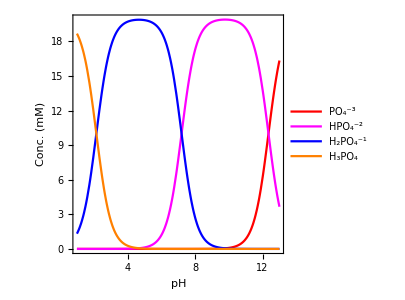

```mathematica
plot1=Plot[Evaluate[10^3{PO4,HPO4,H2PO4,H3PO4}/.sol1/.quant/.Hp-> Quantity[10^-pH,"Molar"]],{pH,1,13},PlotLegends->Placed[LineLegend[{"PO_4^-3","HPO_4^-2","H_2PO_4^-1","H_3PO_4"},Spacings->0.2],{0.75,0.5}],PlotStyle->{Red, Magenta,Blue,Orange},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},AspectRatio->1,Frame-> True,FrameLabel->{"pH","Conc. (mM)"},ImageSize->300]
```

```mathematica
Export[baseDirectory<>"pHConc_pHControl.png",plot1,ImageResolution->300]
```

/Users/abhisheksharma/Desktop/Hybrid_Computation_Final/pHConc_pHControl.png

Considering a constant flux of hydronium ions due to the redox reactions occurring at the electrode in the presence of the redox active species such as quinones (real Current-Voltage relationship can be estimated using the various electrochemical methods such as staircase voltammetry). Assuming two electrons and protons taking part in the redox reaction, the rate of production of hydronium ions is given by,

ⅆH/ⅆt= J/(n F), So if we assume at time t, the amount of H^+added to the mixture is H^*, then we can write the equilibrium equations as,

PO_4^-3+ H^+⇌HPO_4^-2 (K_1)

(C_A- α H^*)                   (C_B+ α H^* - β H^*)

HPO_4^-2+ H^+⇌H_2 PO_4^- (K_2)

(C_B+ α H^* - β H^*)      (C_C+ β H^* - γ H^*)  

H_2 PO_4^-+ H^+⇌H_3 PO_4 (K_3)

 (C_C+ β H^* - γ H^*)              (C_D+ γ H^*)
 
 where C_A,C_B,C_C,C_D are the initial concentration of various species present initially (as calculated above), together with the constraint  α + β +γ  =1.

```mathematica
Clear[cA,cB,cC,cD]
```

```mathematica
eqnx1=K1==(Hp(cA-α HpN))/(cB +α HpN -β HpN);
```

```mathematica
eqnx2=K2==(Hp (cB +α HpN -β HpN))/(cC+β HpN-γ HpN);
```

```mathematica
eqnx3=K3==(Hp(cC+β HpN-γ HpN))/(cD+γ HpN);
```

```mathematica
eqnx4=α+β+γ ==1;
```

Eliminating α, β, γ and then solving H^+is must faster as compared to direct solving... but in principle both works..!

```mathematica
sol2=Solve[Eliminate[{eqnx1,eqnx2,eqnx3,eqnx4},{α,β,γ}], Hp];
```

```mathematica
sol3=Solve[{eqnx1,eqnx2,eqnx3,eqnx4},{α,β,γ, Hp}];
```

As pH is calculated from the concentration units in Molar, here we keep all the units in molar.
https://www.nist.gov/system/files/documents/srd/jpcrd615.pdf

```mathematica
{cA-> icA,cB-> icB,cC-> icC,cD-> icD,K3-> Quantity[10^-pK3,"Molar"],K2->Quantity[10^-pK2,"Molar"],K1->Quantity[10^-pK1,"Molar"]}
```

{cA→3.45607×10^-8 M,cB→0.00773718 M,cC→0.0122626 M,cD→1.73214×10^-7 M,K3→0.00707946 M,K2→6.30957×10^-8 M,K1→4.46684×10^-13 M}

```mathematica
quant={cA-> icA,cB-> icB,cC-> icC,cD-> icD,K3-> Quantity[10^-pK3,"Molar"],K2->Quantity[10^-pK2,"Molar"],K1->Quantity[10^-pK1,"Molar"]}/.q_Quantity:>QuantityMagnitude[q];
```

```mathematica
quant2=Hp-> Quantity[10^-7,"Molar"]/.q_Quantity:>QuantityMagnitude[q];
```

To check, if HpN → 0, we should recover the original equations, which are given by :

```mathematica
Chop[Hp/.sol2/.quant/.HpN-> 0] (* gives three solutions and second solution is correct *)
```

{-0.00197487,1.×10^-7,0}

```mathematica
{eqnx1,eqnx2,eqnx3,eqnx4}
```

{K1==(Hp (cA-HpN α))/(cB+HpN α-HpN β),K2==(Hp (cB+HpN α-HpN β))/(cC+HpN β-HpN γ),K3==(Hp (cC+HpN β-HpN γ))/(cD+HpN γ),α+β+γ==1}

```mathematica
{eqnx1,eqnx2,eqnx3,eqnx4}/.quant
```

{4.46684×10^-13==(Hp (3.45607×10^-8-HpN α))/(0.00773718+HpN α-HpN β),6.30957×10^-8==(Hp (0.00773718+HpN α-HpN β))/(0.0122626+HpN β-HpN γ),0.00707946==(Hp (0.0122626+HpN β-HpN γ))/(1.73214×10^-7+HpN γ),α+β+γ==1}

Looking at this numerically, working precision for small changes is important.

```mathematica
Chop[Hp/.sol2[[2]]/.quant/.HpN-> 1 10^-4,10^-9]
```

1.02135×10^-7

Among α, β, γ most of the contribution comes from β as the starting pH was 7.

```mathematica
Chop[{Hp,α,β,γ}/.sol3[[1]]/.quant/.HpN-> 1 10^-4,10^-9]
```

{1.02135×10^-7,0.0000120528,0.999937,0.0000514127}

```mathematica
out=NSolve[{eqnx1,eqnx2,eqnx3,eqnx4}/.quant/.HpN-> 1 10^-4,{α,β,γ,Hp},Reals,WorkingPrecision->50];out[[3]]
```

NSolve::precw: The precision of the argument function ({4.46684×10^-13-(Hp (3.45607×10^-8-α/10000))/(0.00773718+α/10000-β/10000),6.30957×10^-8-(Hp (0.00773718+α/10000-β/10000))/(0.0122626+β/10000-γ/10000),0.00707946-(Hp (0.0122626+β/10000-γ/10000))/(1.73214×10^-7+γ/10000),-1+α+β+γ}) is less than WorkingPrecision (50).

{α→0.000011598766658260805179433708730002320345804621,β→0.9999369885711550779116848978644480185925508684098,γ→0.000051412662186661283135668426821979087103326969136,Hp→1.021353539624867283614421367270183176054754885078×10^-7}

So, both analytical and numerical solutions seems consistent.

So, all the calculations to estimate the number of moles of hydronium ions (or the concentration in the given volume) generated from the electrolytic current are generated in SI units. Hence, the concentration is in mols/m^3. To update the pH, we convert into mols/dm^3 by multiplying a factor 0.001.

```mathematica
F=UnitConvert[Quantity["FaradayConstant"]]; (* Faraday's Constant *)
```

```mathematica
n=1; (* Number of electrons transferred *)
```

```mathematica
dropletVolume=Quantity[2/3 π (0.5 10^-3)^3 ,"m^3"]; (* Considering a hemispherical droplet region with radii 0.5 mm *)
```

```mathematica
(Quantity[5 10^-6,"Amperes"]Quantity[5,"s"])/(n dropletVolume F) (* concentration of new H+ in SI units *)
```

0.989715 mol/m^3

```mathematica
UnitConvert[(Quantity[5 10^-6,"Amperes"]Quantity[5,"s"])/(n dropletVolume F),"Molar"](* concentration of new H+ in Molar units *)
```

0.000989715 M

Using a factor of 10^-3 from SI units to Molar

```mathematica
hion[iC_,t_]=(Hp/.sol2⟦2⟧/.quant/.HpN->10^-3 QuantityMagnitude[(iC t)/(n dropletVolume F)]); (* A factor of thousand comes from conversion of moles/m^3 to Molar *)
```

```mathematica
Chop[hion[5 10^-6,0.5]]
```

1.02113×10^-7

Checking if the conversion factor works fine.

```mathematica
Chop[Hp/.sol2⟦2⟧/.quant/.HpN->QuantityMagnitude@UnitConvert[(Quantity[5 10^-6 ,"Amperes"] Quantity[0.5,"s"])/(n dropletVolume F),"Molar"]]
```

1.02113×10^-7

So, the conversion factor seems consistent.

Testing creation of protons by applying positive current (to estimate the voltage-time dependence, we can use experimentally derived current-voltage relationship)
Here, we assume that the positive current creates protons and negative current consumes protons.

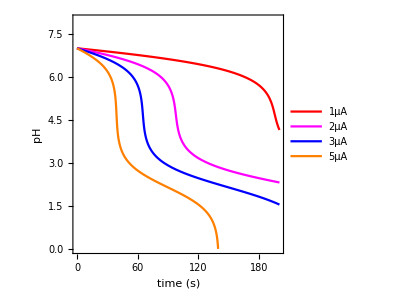

```mathematica
Plot[{-Log[10,Chop@hion[1 10^-6,t]],-Log[10,Chop@hion[2 10^-6,t]],-Log[10,Chop@hion[3 10^-6,t]],-Log[10,Chop@hion[5 10^-6,t]]},{t,0,200},PlotRange-> {0,8},Frame-> True,FrameLabel-> {"time (s)","pH"},Exclusions-> None,PlotLegends->Placed[LineLegend[{"1μA","2μA","3μA","5μA"},Spacings->0.2],{0.15,0.15}],PlotStyle->{Red, Magenta,Blue,Orange},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotLegends-> {"1μA","2μA","3μA","5μA"},AspectRatio->1,ImageSize->300]
```

Instead of solving it analytically, we calculate numerically the pH as a function of applied current and temperature,

```mathematica
hion[iC_,t_]:=Hp/.NSolve[{Eliminate[{eqnx1,eqnx2,eqnx3,eqnx4},{α,β,γ}]/.{HpN->10^-3 QuantityMagnitude[(Quantity[iC,"Amperes"]Quantity[t,"s"])/(n dropletVolume F)]}}/.quant,Hp,WorkingPrecision->Automatic] (* quant consists of initial concentrations of phosphate species, which makes pH=7 automatically.
From the applied current (assuming two electrons take part), to calculate change in pH we introduce the factor 10^-3 
 *)
```

```mathematica
hion[5 10^-6,0.5][[3]]
```

1.02113×10^-7

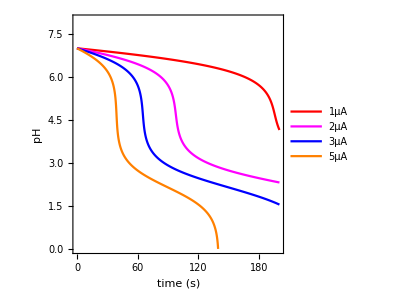

```mathematica
pHPlot1=ListPlot[{Table[{t,-Log[10,hion[1 10^-6,t]⟦3⟧]},{t,0,200,0.2}],Table[{t,-Log[10,hion[2 10^-6,t]⟦3⟧]},{t,0,200,0.2}],Table[{t,-Log[10,hion[3 10^-6,t]⟦3⟧]},{t,0,200,0.2}],Table[{t,-Log[10,hion[5 10^-6,t]⟦3⟧]},{t,0,200,0.2}]},Joined-> True,PlotRange->{0,8},Frame-> True,FrameLabel-> {"time (s)","pH"},PlotLegends->Placed[LineLegend[{"1μA","2μA","3μA","5μA"},Spacings->0.2],{0.15,0.15}],PlotStyle->{Red, Magenta,Blue,Orange},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},AspectRatio->1,ImageSize->300]
```

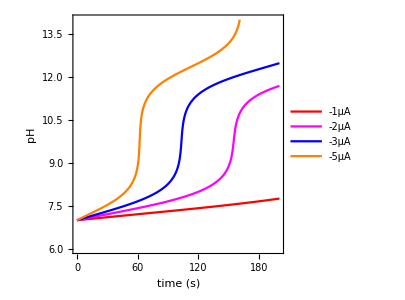

```mathematica
pHPlot2=ListPlot[{Table[{t,-Log[10,hion[-1 10^-6,t]⟦3⟧]},{t,0,200,0.2}],Table[{t,-Log[10,hion[-2 10^-6,t]⟦3⟧]},{t,0,200,0.2}],Table[{t,-Log[10,hion[-3 10^-6,t]⟦3⟧]},{t,0,200,0.2}],Table[{t,-Log[10,hion[-5 10^-6,t]⟦3⟧]},{t,0,200,0.2}]},Joined-> True,PlotRange->{6,14},Frame-> True,FrameLabel-> {"time (s)","pH"},PlotLegends->Placed[LineLegend[{"-1μA","-2μA","-3μA","-5μA"},Spacings->0.2],{0.15,0.8}],PlotStyle->{Red, Magenta,Blue,Orange},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},AspectRatio->1,ImageSize->300]
```

```mathematica
Export[baseDirectory<>"pHPlot1_pHControl.png",pHPlot1,ImageResolution->300]
```

/Users/abhisheksharma/Desktop/Hybrid_Computation_Final/pHPlot1_pHControl.png

```mathematica
Export[baseDirectory<>"pHPlot2_pHControl.png",pHPlot2,ImageResolution->300]
```

/Users/abhisheksharma/Desktop/Hybrid_Computation_Final/pHPlot2_pHControl.png

So, the numerical approach is more stable and works reliably for negative and positive currents.

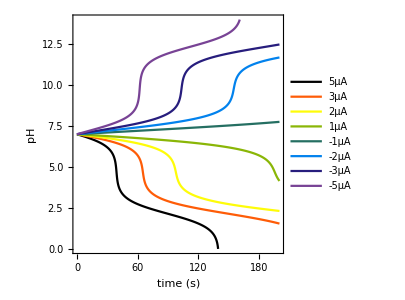

```mathematica
pHPlot=ListPlot[{Table[{t,-Log[10,hion[5 10^-6,t]⟦3⟧]},{t,0,200,0.2}],Table[{t,-Log[10,hion[3 10^-6,t]⟦3⟧]},{t,0,200,0.2}],Table[{t,-Log[10,hion[2 10^-6,t]⟦3⟧]},{t,0,200,0.2}],Table[{t,-Log[10,hion[1 10^-6,t]⟦3⟧]},{t,0,200,0.2}],Table[{t,-Log[10,hion[-1 10^-6,t]⟦3⟧]},{t,0,200,0.2}],Table[{t,-Log[10,hion[-2 10^-6,t]⟦3⟧]},{t,0,200,0.2}],Table[{t,-Log[10,hion[-3 10^-6,t]⟦3⟧]},{t,0,200,0.2}],Table[{t,-Log[10,hion[-5 10^-6,t]⟦3⟧]},{t,0,200,0.2}]},Joined-> True,PlotRange->{0,14},Frame-> True,FrameLabel-> {"time (s)","pH"},PlotStyle->ColorData[3,"ColorList"],AspectRatio->1,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotLegends-> {"5μA","3μA","2μA","1μA","-1μA","-2μA","-3μA","-5μA"},ImageSize->300]
```

#### Calculating pH by time stepping current with defined time interval

For numerical solution, coupling with the electrochemical kinetics, we define a pH update function which updates the pH and local buffer concentrations using time stepping.

```mathematica
Unprotect[$MachinePrecision];
$MachinePrecision=50; (* Setting the Machine Precision for stability while using NSolve *)
Protect[$MachinePrecision];
```

```mathematica
icAM = QuantityMagnitude@icA;icBM = QuantityMagnitude@icB;icCM = QuantityMagnitude@icC;icDM = QuantityMagnitude@icD;
```

```mathematica
pHdropletUpdate[appC_,Δt_,{cA_,cB_,cC_,cD_}]:=Module[{eqn1,eqn2,eqn3,eqn4,quant,soln,HpNC},
(*  
   Note that pH calculations are always performed in SI units and then pH is updated with a correction factor 10^-3.
  -> appC : applied current 
 -> Δt : time interval
-> {cA, cB, cC, cD} : Initial Concentration of four phosphate species 
*)
eqn1[cA,cB,cC,cD]:=K1==(Hp (cA-α HpN))/(cB +α HpN -β HpN);
eqn2[cA,cB,cC,cD]:=K2==(Hp (cB +α HpN -β HpN))/(cC+β HpN-γ HpN);
eqn3[cA,cB,cC,cD]:=K3==(Hp (cC+β HpN-γ HpN))/(cD+γ HpN);
eqn4=α+β+γ ==1.;
quant ={K3->10^-pK3,K2->10^-pK2,K1->10^-pK1}; 
HpNC=10^-3 QuantityMagnitude[(Quantity[appC,"Amperes"]Quantity[Δt,"s"])/(n dropletVolume F)];  
soln=NSolve[({eqn1[cA,cB,cC,cD],eqn2[cA,cB,cC,cD],eqn3[cA,cB,cC,cD],eqn4}/.HpN->HpNC/.quant)/.q_Quantity:>QuantityMagnitude[q],{Hp,α,β,γ},WorkingPrecision->100];Chop[{-Log[10,Hp],cA-α HpNC,cB +α HpNC -β HpNC,cC+β HpNC-γ HpNC,cD+γ HpNC}/.soln⟦3⟧]]
```

```mathematica
{icAM,icBM,icCM,icDM}
```

{3.45607×10^-8,0.00773718,0.0122626,1.73214×10^-7}

```mathematica
x=pHdropletUpdate[5 10^-6,0.5,{icAM,icBM,icCM,icDM}];10^(-x[[1]])
```

NSolve::precw: The precision of the argument function ({4.46684×10^-13-(Hp (3.45607×10^-8-0.0000989715 α))/(0.00773718+0.0000989715 α-0.0000989715 β),6.30957×10^-8-(Hp (0.00773718+«23» α-0.0000989715 β))/(0.0122626+0.0000989715 β-0.0000989715 γ),0.00707946-(«1»)/(«1»),-1.+α+β+γ}) is less than WorkingPrecision (100).

1.02113106986955625957539056723009630270382865103488994115849646093629103598386761208674468954450767×10^-7

```mathematica
Quiet[pHdropletUpdate[ 1 10^-6,500,{icAM,icBM,icCM,icDM}]];(* Testing pH updating function *)
```

```mathematica
cA=icAM;cB=icBM;cC=icCM;cD=icDM;
```

```mathematica
data1=Quiet[Monitor[Table[Block[{out},out=pHdropletUpdate[ 3 10^-6,1,{cA,cB,cC,cD}];cA=out⟦2⟧;cB=out⟦3⟧;cC=out⟦4⟧;cD=out⟦5⟧;
out],{i,0.1,200}],i]];
```

```mathematica
cA=icAM;cB=icBM;cC=icCM;cD=icDM;
```

```mathematica
data2=Quiet[Monitor[Table[Block[{out},out=pHdropletUpdate[ -2 10^-6,1,{cA,cB,cC,cD}];cA=out⟦2⟧;cB=out⟦3⟧;cC=out⟦4⟧;cD=out⟦5⟧;
out],{i,0.1,200}],i]];
```

```mathematica
pTest1=ListPlot[data1⟦All,1⟧,PlotRange->{2,8},Joined-> True,PlotStyle->{Black,Dashed},PlotStyle-> Automatic,AspectRatio->1,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},FrameLabel->{"Time(s)","pH"},Frame->True,ImageSize->300];
```

```mathematica
pTest2=ListPlot[data2⟦All,1⟧,PlotRange->{6,14},Joined-> True,PlotStyle->{Black,Dashed},PlotStyle-> Automatic,AspectRatio->1,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},FrameLabel->{"Time(s)","pH"},Frame->True,ImageSize->300];
```

Checking the overlap, to be sure that the function is correct.

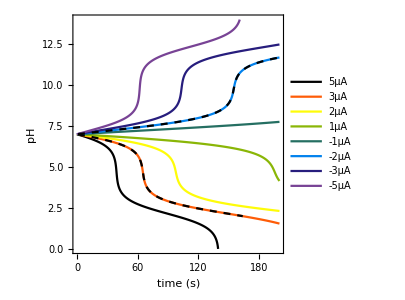

```mathematica
Show[{pHPlot,pTest1,pTest2}]
```

Oscillating the current value for up to 10 cycles,

```mathematica
currentT =Flatten@Table[{ Table[-5 10^-6,{t,10}],Table[5 10^-6,{t,15}]},{i,10}];
```

```mathematica
cA=icAM;cB=icBM;cC=icCM;cD=icDM;
```

```mathematica
data=Quiet[Monitor[Table[Block[{out},out=pHdropletUpdate[currentT⟦i⟧,1,{cA,cB,cC,cD}];cA=out⟦2⟧;cB=out⟦3⟧;cC=out⟦4⟧;cD=out⟦5⟧;
out],{i,1,Length[currentT]}],i]];
```

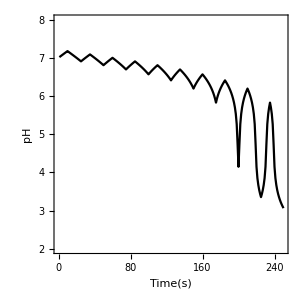

```mathematica
ListPlot[data⟦All,1⟧,PlotStyle->Black,PlotRange->{2,8},Joined-> True,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},AspectRatio->1,Frame->True,FrameLabel->{"Time(s)","pH"},ImageSize->300]
```

The numerical scheme seems to work fine and updating pH using time-stepping logic.

## Programmable pH changes together with control logic

Controls the pH inside the droplet using redox chemistry as described in the previous section, for programmable chemical reactions.

```mathematica
eq1=K1==(Hp PO4)/HPO4;
```

```mathematica
eq2=K2==(Hp HPO4)/H2PO4;
```

```mathematica
eq3=K3==(Hp H2PO4)/H3PO4;
```

```mathematica
eq4=PO4+HPO4+H2PO4+H3PO4==iHPO4;
```

```mathematica
soln=Solve[{eq1,eq2,eq3,eq4},{PO4,HPO4,H2PO4,H3PO4}];
```

```mathematica
soln//First
```

{PO4→(iHPO4 K1 K2 K3)/(Hp^3+Hp^2 K3+Hp K2 K3+K1 K2 K3),HPO4→(Hp iHPO4 K2 K3)/(Hp^3+Hp^2 K3+Hp K2 K3+K1 K2 K3),H2PO4→(Hp^2 iHPO4 K3)/(Hp^3+Hp^2 K3+Hp K2 K3+K1 K2 K3),H3PO4→(Hp^3 iHPO4)/(Hp^3+Hp^2 K3+Hp K2 K3+K1 K2 K3)}

```mathematica
controlpH[pHValue_,initpH_,Δt_,totalPhosphate_,currentMag_,totalTime_]:= Module[{icA,icB,icC,icD,cA,cB,cC,cD,out,tSteps,currentPolarity,cCurrent,data},
(* 
   pHValue: pH value to be sustained,
   initpH: starting pH value,
   Δt: Time stepping for switching potentials,
   totalPhosphate: Total concentration of various phosphate species,
   currentMag: Magnitude of the applied current (in SI units),
   totalTime: Total time of the simulation (in seconds)
*)
(* Calculating concentration of various phosphate species based on inital pH value *)
quant = {iHPO4-> Quantity[totalPhosphate,"Molar"],K3-> Quantity[10^-pK3,"Molar"],K2->Quantity[10^-pK2,"Molar"],K1->Quantity[10^-pK1,"Molar"]}; 
quant2=Hp-> Quantity[10^-initpH,"Molar"];
{icA,icB,icC,icD}={PO4,HPO4,H2PO4,H3PO4}/.soln/.quant/.quant2//Flatten; (* Initial variables *)
cA=icA;cB=icB;cC=icC;cD=icD; (* Time dependent variables *)
tSteps=IntegerPart@(totalTime/Δt);(* Total number of the steps *)
out={initpH,cA,cB,cC,cD};
data=Quiet[Monitor[Table[Block[{},
currentPolarity=If[out⟦1⟧>pHValue,1,-1];
out=pHdropletUpdate[currentPolarity currentMag,Δt,{cA,cB,cC,cD}];
cA=out⟦2⟧;cB=out⟦3⟧;cC=out⟦4⟧;cD=out⟦5⟧;
out],{i,1,tSteps}],i]];data]
```

Trying to sustain certain pH using simple Finite State Logic at different applied currents.

```mathematica
dataF=Table[controlpH[9.,6.5,1.,5 10^-3,i 10^-6,300],{i,5,1,-1}];
```

```mathematica
Dimensions/@dataF
```

{{300,5},{300,5},{300,5},{300,5},{300,5}}

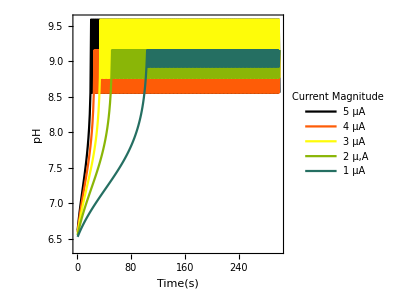

```mathematica
plot2=ListPlot[dataF⟦All,All,1⟧,Joined-> True,PlotRange->All,Joined-> True,AspectRatio->1,PlotStyle->ColorData[3,"ColorList"],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},Frame->True,FrameLabel->{"Time(s)","pH"},PlotLegends->Placed[LineLegend[{"5 μA","4 μA","3 μA","2 μ,A","1 μA"},Spacings->0.2,LegendLabel->"Current Magnitude"],{0.75,0.23}],ImageSize->300]
```

```mathematica
Export[baseDirectory<>"pHControl1.png",plot2,ImageResolution->300]
```

/Users/abhisheksharma/Desktop/Hybrid_Computation_Final/pHControl1.png

Trying to sustain certain pH using simple Finite State Logic in the absence of dissipation and droplet-droplet coupling

```mathematica
dataF=Table[controlpH[i,6.5,1.,5 10^-3,2 10^-6,300],{i,2,12}];
```

```mathematica
Dimensions/@dataF
```

{{300,5},{300,5},{300,5},{300,5},{300,5},{300,5},{300,5},{300,5},{300,5},{300,5},{300,5}}

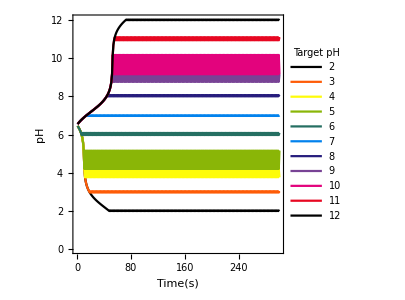

```mathematica
plot3=ListPlot[dataF⟦All,All,1⟧,Joined-> True,PlotRange->All,Joined-> True,PlotStyle->ColorData[3,"ColorList"],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},Frame->True,FrameLabel->{"Time(s)","pH"},AspectRatio->1,PlotLegends->Placed[LineLegend[Range[2,12],Spacings->0.1,LegendLayout->"Row",LegendLabel->"Target pH"],{0.5,0.08}],ImageSize->300]
```

```mathematica
Export[baseDirectory<>"pHControl2.png",plot3,ImageResolution->300]
```

/Users/abhisheksharma/Desktop/Hybrid_Computation_Final/pHControl2.png

Trying to sustain certain pH using simple Finite State Logic at different buffer concentrations  in the absence of dissipation and droplet - droplet coupling

```mathematica
dataF=Table[controlpH[9.,6.5,1.,i 5 10^-3,5 10^-6,600],{i,1,10}];
```

```mathematica
Dimensions/@dataF
```

{{600,5},{600,5},{600,5},{600,5},{600,5},{600,5},{600,5},{600,5},{600,5},{600,5}}

```mathematica
Table[ToString[i 5]<>" mM",{i,1,10}]
```

{5 mM,10 mM,15 mM,20 mM,25 mM,30 mM,35 mM,40 mM,45 mM,50 mM}

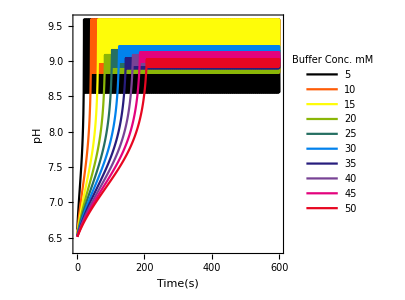

```mathematica
plot4=ListPlot[dataF⟦All,All,1⟧,Joined-> True,PlotRange->All,Joined-> True,PlotStyle->ColorData[3,"ColorList"],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},Frame->True,FrameLabel->{"Time(s)","pH"},AspectRatio->1,PlotLegends->Placed[LineLegend[Table[ToString[i 5],{i,1,10}],Spacings->0.2,LegendLayout->"Row",LegendLabel->"Buffer Conc. mM"],{0.55,0.15}],ImageSize->300]
```

```mathematica
Export[baseDirectory<>"pHControl3.png",plot4,ImageResolution->300]
```

/Users/abhisheksharma/Desktop/Hybrid_Computation_Final/pHControl3.png

## Two dimensional spatio-temporal dynamics in an array of localized electrolyte-electrode pairs

Here, we implement local pH changes due to the current flowing through the system in the presence of the buffered system, following the same dynamics as described in the previous section.

```mathematica
ClearAll["Global`*"]
```

```mathematica
SeedRandom[110]
```

RandomGeneratorState[…]

```mathematica
baseDirectory=NotebookDirectory[]
```

/Users/abhisheksharma/Desktop/Hybrid_Computation_Final/

```mathematica
e=UnitConvert[Quantity["ElementaryCharge"]]; (* Electronic Charge *)
```

```mathematica
NA=UnitConvert[Quantity["AvogadroConstant"]]; (* Avogadro's Constant *)
```

```mathematica
kB=UnitConvert[Quantity["BoltzmannConstant"]]; (* Boltzmann's Constant *)
```

```mathematica
F=UnitConvert[Quantity["FaradayConstant"]]; (* Faraday's Constant *)
```

```mathematica
R=UnitConvert[Quantity["MolarGasConstant"]]; (* Molar Gas Constant *)
```

```mathematica
T=Quantity[298.,"K"]; (* Working Temperature *)
```

```mathematica
elecRadius=UnitConvert@Quantity[1.0,"mm"] ;(* Radius of electrode *)
```

```mathematica
elecGap=UnitConvert@Quantity[1.0,"mm"];(* Gap between two nearby electrodes, defined from edge to edge *)
```

```mathematica
dropHeight=UnitConvert@Quantity[1.0,"mm"]; (* Height of the droplet above electrode array *)
```

```mathematica
dropletVolume = UnitConvert[π(elecRadius+1/2 elecGap)^2 dropHeight,"m^3"];(* Volume of the droplet based on the height and electrode dimensions *)
```

```mathematica
CBack=UnitConvert@Quantity[100 10^-3,"Molar"]; (* Concentration of background supporting electrolyte *)
```

```mathematica
CEl=UnitConvert@Quantity[100 10^-3,"Molar"]; (* Concentration of electroactive species *)
```

```mathematica
ϵ0=UnitConvert@Quantity["VacuumPermittivity"];
```

```mathematica
ϵ=80.0; (* Dielectric Constrant of water *)
```

```mathematica
CDL=UnitConvert[Quantity[20.,"μF/cm^2"],"F/m^2"](* Assumed Typical Value inspired from Helmholtz Model 20μF/cm^2: Double Layer capacitance per unit area
https://edisciplinas.usp.br/pluginfile.php/4283018/mod_resource/content/1/Double_layer.pdf *)
```

0.2 F/m^2

```mathematica
𝒟=UnitConvert@Quantity[1.0 10^-9,"m^2/s"]; (* Diffusion constant of supporting electrolyte *)
```

```mathematica
𝒟ϵ=UnitConvert@Quantity[1.0 10^-9,"m^2/s"]; (* Diffusion constant of electroactive system *)
```

```mathematica
khom=UnitConvert@Quantity[2.5 10^-6,"m/s"];(* Homogeneous rate constant for the chemical reaction : Assumed value for the model (independent of Quinone electrochemistry) *)
```

```mathematica
z=1;(* Valence of background supporting electrolyte *)
```

```mathematica
λD=√((ϵ ϵ0 kB T)/(2 z^2 e^2 CBack NA)) (* Double Layer Length, 
Diffuse-charge dynamics in electrochemical systems, Bazant et al, Phys.Rev.E 70,021506,
https://doi.org/10.1103/PhysRevE.70.021506*)
```

9.70886×10^-10 m

```mathematica
n=1;(* Number of electrons involved in electrochemical reaction *)
```

```mathematica
BulkCond= (2 z^2 e^2 CBack NA 𝒟)/(kB T)//UnitSimplify (* Bulk Electrolytic Conductivity for symmetric electrolyte, 
Diffuse-charge dynamics in electrochemical systems, Bazant et al, Phys.Rev.E 70,021506,
https://doi.org/10.1103/PhysRevE.70.021506 *)
```

0.751454 per meterper ohm

Using the bulk conductivity, we calculate the three resistances used in the local electrolyte-electrode pair model. These are just the basic approximations and can be updated with more details. 

1. R_B0=1/σ h/(π r^2) : This resistance connects the electrode to the height of the gel electrolyte (assumed). So, the length of the resistance is h/2 and area is the area of the electrode π r^2. This is just an approximation to the vertical resistance from the electrode to center of the electrolyte, where we assume that the vertical current flows up to half the height.

2. R_B=1/σ r/(2 r h): This resistance is the horizontal resistance from the center of the electrode at the height h/2 to the edge of the electrode. So, the length of the resistance is the electrode radius and the area of the cross section is 2 r x h

3. R_B=1/σ g/(2 r h): This resistance is the horizontal resistance from  the edge of the one electrode to the edge of other electrode. So, the length of the resistance is the gap between two electrodes and the area of the cross section is 2 r x h

```mathematica
dropletBulkR0=1/BulkCond dropHeight/(π elecRadius^2)
```

423.592 Ω

```mathematica
dropletBulkR=1/BulkCond elecRadius/(2 elecRadius dropHeight)
```

665.377 Ω

```mathematica
dropletBulkInt=1/BulkCond elecGap/(2 elecRadius dropHeight)
```

665.377 Ω

```mathematica
iLim= UnitConvert[F 𝒟ϵ CBack/elecGap,"A/m^2"]; (* Limiting current density *)
```

```mathematica
limitingCurrent =UnitConvert[π elecRadius^2 F 𝒟ϵ CBack/elecGap,"A"] (* Diffusion limited current flowing through the electrode *)
```

0.0000303118 A

```mathematica
j0[cOx_,cRe_,k0_]:= F k0 cOx^β cRe^(1-β)
```

```mathematica
ExCurrentDensity =UnitConvert[FullSimplify[ j0[CEl,CEl,khom]],"A/m^2"]
```

24.1213 A/m^2

```mathematica
ExCurrentDensity/iLim
```

2.5

#### Buffer Kinetics Parameters

```mathematica
eq1=K1==(Hp PO4)/HPO4;
```

```mathematica
eq2=K2==(Hp HPO4)/H2PO4;
```

```mathematica
eq3=K3==(Hp H2PO4)/H3PO4;
```

```mathematica
eq4=PO4+HPO4+H2PO4+H3PO4==iHPO4;
```

```mathematica
sol1=Solve[{eq1,eq2,eq3,eq4},{PO4,HPO4,H2PO4,H3PO4}];
```

```mathematica
{PO4,HPO4,H2PO4,H3PO4}/.sol1//Flatten
```

{(iHPO4 K1 K2 K3)/(Hp^3+Hp^2 K3+Hp K2 K3+K1 K2 K3),(Hp iHPO4 K2 K3)/(Hp^3+Hp^2 K3+Hp K2 K3+K1 K2 K3),(Hp^2 iHPO4 K3)/(Hp^3+Hp^2 K3+Hp K2 K3+K1 K2 K3),(Hp^3 iHPO4)/(Hp^3+Hp^2 K3+Hp K2 K3+K1 K2 K3)}

```mathematica
totalPhosphate= Quantity[20 10^-3,"Molar"]; (* Total Phosphate Concentration *)
```

```mathematica
pK3 = 2.15; (* Phosphate Buffer pK3 *)
```

```mathematica
pK2=7.2; (* Phosphate Buffer pK2 *)
```

```mathematica
pK1= 12.35; (* Phosphate Buffer pK1 *)
```

```mathematica
quant = {iHPO4-> totalPhosphate,K3-> Quantity[10^-pK3,"Molar"],K2->Quantity[10^-pK2,"Molar"],K1->Quantity[10^-pK1,"Molar"]}; (* Assuming initial pH is 7 *)
```

```mathematica
quant2=Hp-> Quantity[10^-7,"Molar"];
```

So, initial percent of all the species :

```mathematica
({PO4,HPO4,H2PO4,H3PO4}/iHPO4)/.sol1/.quant/.quant2//Flatten
```

{1.72804×10^-6,0.386859,0.61313,8.6607×10^-6}

```mathematica
{icA,icB,icC,icD}={PO4,HPO4,H2PO4,H3PO4}/.sol1/.quant/.quant2//Flatten
```

{3.45607×10^-8 M,0.00773718 M,0.0122626 M,1.73214×10^-7 M}

```mathematica
Unprotect[$MachinePrecision];
$MachinePrecision=50;
Protect[$MachinePrecision];
```

```mathematica
icAM = QuantityMagnitude@icA;icBM = QuantityMagnitude@icB;icCM = QuantityMagnitude@icC;icDM = QuantityMagnitude@icD;
```

```mathematica
pHdropletUpdate[appC_,Δt_,{cA_,cB_,cC_,cD_}]:=Module[{eqn1,eqn2,eqn3,eqn4,quant,soln,HpNC},
(*  
   -> appC : applied current 
 -> Δt : time interval
-> {cA, cB, cC, cD} : Initial Concentration of four phosphate species 
*)
eqn1[cA,cB,cC,cD]:=K1==(Hp (cA-α HpN))/(cB +α HpN -β HpN);
eqn2[cA,cB,cC,cD]:=K2==(Hp (cB +α HpN -β HpN))/(cC+β HpN-γ HpN);
eqn3[cA,cB,cC,cD]:=K3==(Hp (cC+β HpN-γ HpN))/(cD+γ HpN);
eqn4=α+β+γ ==1.;
quant ={K3->10^-pK3,K2->10^-pK2,K1->10^-pK1}; 
HpNC=10^-3 QuantityMagnitude[(Quantity[appC,"Amperes"]Quantity[Δt,"s"])/(n dropletVolume F)];  
soln=NSolve[({eqn1[cA,cB,cC,cD],eqn2[cA,cB,cC,cD],eqn3[cA,cB,cC,cD],eqn4}/.HpN->HpNC/.quant)/.q_Quantity:>QuantityMagnitude[q],{Hp,α,β,γ},WorkingPrecision->100];Chop[{-Log[10,Hp],cA-α HpNC,cB +α HpNC -β HpNC,cC+β HpNC-γ HpNC,cD+γ HpNC}/.soln⟦3⟧]]
```

```mathematica
{icAM,icBM,icCM,icDM}
```

{3.45607×10^-8,0.00773718,0.0122626,1.73214×10^-7}

```mathematica
x=Quiet[pHdropletUpdate[5 10^-6,0.5,{icAM,icBM,icCM,icDM}]];10^(-x[[1]])(* Testing pH updating function *)
```

1.00077298859591523586821022312408079446184780859236509521406580576750219228682605653116049854196187×10^-7

```mathematica
(*
(* For testing accuracy : works fine *)
Clear[cA,cB,cC,cD]
eqnx1=K1==(Hp(cA-α HpN))/(cB +α HpN -β HpN);
eqnx2=K2==(Hp (cB +α HpN -β HpN))/(cC+β HpN-γ HpN);
eqnx3=K3==(Hp(cC+β HpN-γ HpN))/(cD+γ HpN);
eqnx4=α+β+γ ==1;
sol2=Solve[Eliminate[{eqnx1,eqnx2,eqnx3,eqnx4},{α,β,γ}], Hp];
Chop[(Hp/.sol2⟦2⟧/.(quant/.q_Quantity:>QuantityMagnitude[q])/.{cA->icAM,cB->icBM,cC->icCM,cD->icDM}/.HpN->10^-3 QuantityMagnitude[(Quantity[5 10^-6,"Amperes"]Quantity[0.5,"s"])/(n dropletVolume F)])]
*)
```

```mathematica
cA=icAM;cB=icBM;cC=icCM;cD=icDM;
```

```mathematica
data=Quiet[Monitor[Table[Block[{out},out=pHdropletUpdate[5 10^-5,1,{cA,cB,cC,cD}];cA=out⟦2⟧;cB=out⟦3⟧;cC=out⟦4⟧;cD=out⟦5⟧;
out],{i,0.01,200}],i]];
```

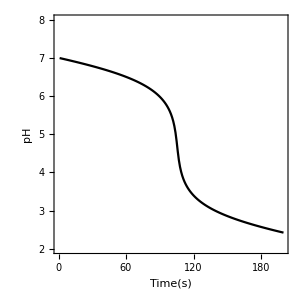

```mathematica
ListPlot[data⟦All,1⟧,PlotRange->{2,8},Joined-> True,PlotStyle->Black,PlotStyle-> Automatic,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},Frame->True,FrameLabel->{"Time(s)","pH"},AspectRatio->1,ImageSize->300]
```

#### Governing equations for multi-electrode array network

Creates network equations for n x n droplet array with time dependent electrode potentials.

```mathematica
fVShift[{V1_,V2_},{λ_,t0_},t_]:=V1+(V2-V1)(1/2+1/π ArcTan[(t-t0)/λ])
```

```mathematica
droplet2DBV[i_,j_,K_,tS_]:=Module[{indexStr,eq1,eq2,eq3,eq4,eq5,eq6,eq7,vars},
indexStr=ToString[i]<>"s"<>ToString[j];
eq1=Symbol["i"<>indexStr<>"N"][t]+Symbol["i"<>indexStr<>"E"][t]+Symbol["i"<>indexStr<>"S"][t]+Symbol["i"<>indexStr<>"W"][t]==Symbol["iEL"<>indexStr][t];
eq2=Symbol["iEL"<>indexStr][t]==AreaEL Cdl D[Evaluate[fVShift[{ Symbol["Vi"<>indexStr],Symbol["Vf"<>indexStr]},{λ,tS},t]-Symbol["ϕ"<>indexStr][t]-E0],t]+Evaluate[AreaEL i0(Exp[(αa n F ηm)/(R T)]-Exp[-(αc n F ηm)/(R T)])/.ηm-> Evaluate[fVShift[{Symbol["Vi"<>indexStr],Symbol["Vf"<>indexStr]},{λ,tS},t]-Symbol["ϕ"<>indexStr][t]-E0]];
eq3=Symbol["ϕ"<>indexStr][t]-Symbol["ϕP"<>indexStr][t]==RBulkA Symbol["iEL"<>indexStr][t];
eq4=Symbol["ϕP"<>indexStr][t]-Symbol["ϕPN"<>indexStr][t]==RBulkB Symbol["i"<>indexStr<>"N"][t];
eq5=Symbol["ϕP"<>indexStr][t]-Symbol["ϕPE"<>indexStr][t]==RBulkB Symbol["i"<>indexStr<>"E"][t];
eq6=Symbol["ϕP"<>indexStr][t]-Symbol["ϕPS"<>indexStr][t]==RBulkB Symbol["i"<>indexStr<>"S"][t];
eq7=Symbol["ϕP"<>indexStr][t]-Symbol["ϕPW"<>indexStr][t]==RBulkB Symbol["i"<>indexStr<>"W"][t];

vars={Symbol["i"<>indexStr<>"N"][t],Symbol["i"<>indexStr<>"E"][t],Symbol["i"<>indexStr<>"S"][t],Symbol["i"<>indexStr<>"W"][t],Symbol["iEL"<>indexStr][t],Symbol["ϕ"<>indexStr][t],Symbol["ϕP"<>indexStr][t],Symbol["ϕPN"<>indexStr][t],Symbol["ϕPE"<>indexStr][t],Symbol["ϕPS"<>indexStr][t],Symbol["ϕPW"<>indexStr][t]};{{eq1,eq2,eq3,eq4,eq5,eq6,eq7},vars}]
```

```mathematica
dropletConnections2D[i_,j_,K_]:=Module[{indexStr,eq1,eq2,eq3,eq4,eq5,eq6,vars}, 
indexStr=ToString[i]<>"s"<>ToString[j];
eq1=Symbol["iCN"<>indexStr][t]==Symbol["i"<>ToString[i]<>"s"<>ToString[j]<>"N"][t];
eq2=Symbol["iCN"<>indexStr][t]==-Symbol["i"<>ToString[i]<>"s"<>ToString[j+1]<>"S"][t]; 
eq3=Symbol["iCE"<>indexStr][t]==Symbol["i"<>ToString[i]<>"s"<>ToString[j]<>"E"][t];
eq4=Symbol["iCE"<>indexStr][t]==-Symbol["i"<>ToString[i+1]<>"s"<>ToString[j]<>"W"][t];
eq5=Symbol["ϕPN"<>indexStr][t]-Symbol["ϕPS"<>ToString[i]<>"s"<>ToString[j+1]][t]== RConn Symbol["iCN"<>indexStr][t];
eq6=Symbol["ϕPE"<>indexStr][t]-Symbol["ϕPW"<>ToString[i+1]<>"s"<>ToString[j]][t]== RConn Symbol["iCE"<>indexStr][t];

vars={Symbol["iCN"<>indexStr][t],Symbol["iCE"<>indexStr][t]};
{{eq1,eq2,eq3,eq4,eq5,eq6},vars}]
```

```mathematica
dropletEndConnections2D[K_]:=Module[{eqSet1,eqSet2,eqSet3,eqSet4,eqSet5,eqSet6,eqSet7,eqSet8,eqSet9,eqSet10,eqSet11,eqSet12,eqSet13,eqSet14,vars},
(* --- Left Column --- *)
eqSet1=Table[Symbol["iCW1"<>"s"<>ToString[j]][t]==Symbol["i1"<>"s"<>ToString[j]<>"W"][t],{j,1,K}];
eqSet2=Table[Symbol["ϕPW1"<>"s"<>ToString[j]][t]==RConn Symbol["i1"<>"s"<>ToString[j]<>"W"][t],{j,1,K}];

(* --- Bottom Row --- *)
eqSet3=Table[Symbol["iCS"<>ToString[j]<>"s"<>"1"][t]==Symbol["i"<>ToString[j]<>"s"<>"1S"][t],{j,1,K}];
eqSet4=Table[Symbol["ϕPS"<>ToString[j]<>"s"<>"1"][t]==RConn Symbol["i"<>ToString[j]<>"s"<>"1S"][t],{j,1,K}];

(* --- Right Column --- *)
eqSet5=Table[Symbol["iCE"<>ToString[K]<>"s"<>ToString[j]][t]==Symbol["i"<>ToString[K]<>"s"<>ToString[j]<>"E"][t],{j,1,K}];
eqSet6=Table[Symbol["ϕPE"<>ToString[K]<>"s"<>ToString[j]][t]== RConn Symbol["i"<>ToString[K]<>"s"<>ToString[j]<>"E"][t],{j,1,K}];

eqSet7=Table[Symbol["iCN"<>ToString[K]<>"s"<>ToString[j]][t]==Symbol["i"<>ToString[K]<>"s"<>ToString[j]<>"N"][t],{j,1,K-1}];
eqSet8=Table[Symbol["iCN"<>ToString[K]<>"s"<>ToString[j]][t]==-Symbol["i"<>ToString[K]<>"s"<>ToString[j+1]<>"S"][t],{j,1,K-1}];
eqSet9=Table[Symbol["ϕPN"<>ToString[K]<>"s"<>ToString[j]][t]-Symbol["ϕPS"<>ToString[K]<>"s"<>ToString[j+1]][t]== RConn Symbol["i"<>ToString[K]<>"s"<>ToString[j]<>"N"][t],{j,1,K-1}];

(* --- Top Row --- *)
eqSet10=Table[Symbol["iCN"<>ToString[j]<>"s"<>ToString[K]][t]==Symbol["i"<>ToString[j]<>"s"<>ToString[K]<>"N"][t],{j,1,K}];
eqSet11=Table[Symbol["ϕPN"<>ToString[j]<>"s"<>ToString[K]][t]==RConn Symbol["i"<>ToString[j]<>"s"<>ToString[K]<>"N"][t],{j,1,K}];

eqSet12=Table[Symbol["iCE"<>ToString[j]<>"s"<>ToString[K]][t]==Symbol["i"<>ToString[j]<>"s"<>ToString[K]<>"E"][t],{j,1,K-1}];
eqSet13=Table[Symbol["iCE"<>ToString[j]<>"s"<>ToString[K]][t]==-Symbol["i"<>ToString[j+1]<>"s"<>ToString[K]<>"W"][t],{j,1,K-1}];
eqSet14=Table[Symbol["ϕPE"<>ToString[j]<>"s"<>ToString[K]][t]-Symbol["ϕPW"<>ToString[j+1]<>"s"<>ToString[K]][t]== RConn Symbol["i"<>ToString[j]<>"s"<>ToString[K]<>"E"][t],{j,1,K-1}];

vars={Table[Symbol["iCW1"<>"s"<>ToString[j]][t],{j,1,K}],
           Table[Symbol["iCS"<>ToString[j]<>"s"<>"1"][t],{j,1,K}],
           Table[Symbol["iCE"<>ToString[K]<>"s"<>ToString[j]][t],{j,1,K}],
           Table[Symbol["iCN"<>ToString[K]<>"s"<>ToString[j]][t],{j,1,K}],
           Table[Symbol["iCN"<>ToString[j]<>"s"<>ToString[K]][t],{j,1,K-1}],
           Table[Symbol["iCE"<>ToString[j]<>"s"<>ToString[K]][t],{j,1,K-1}]};
{{eqSet1,eqSet2,eqSet3,eqSet4,eqSet5,eqSet6,eqSet7,eqSet8,eqSet9,eqSet10,eqSet11,eqSet12,eqSet13,eqSet14}//Flatten,vars//Flatten}]
```

```mathematica
eqns[N_,t0_]:=Flatten[Table[droplet2DBV[i,j,N,t0],{i,1,N},{j,1,N}],1] (* Electrochemical Kinetics Description *)
```

```mathematica
eqnsCon[N_]:=Flatten[Table[dropletConnections2D[i,j,N],{i,1,N-1},{j,1,N-1}],1] (* Connections between Droplets *)
```

```mathematica
eqnsEndCon[N_]:=dropletEndConnections2D[N] (* Connections between droplets at the boundaries *)
```

```mathematica
nEl=10;  (* Number of electrodes along X/Y *)
```

```mathematica
eqLen1=Total@{Length[Union@Flatten@eqns[nEl,tS]⟦All,1⟧],Length[Union@Flatten@eqnsCon[nEl]⟦All,1⟧],Length[Union@dropletEndConnections2D[nEl]⟦1⟧]};
eqLen2=Total@{Length[Union@Flatten@eqns[nEl,tS]⟦All,2⟧],Length[Union@Flatten@eqnsCon[nEl]⟦All,2⟧],Length[Union@dropletEndConnections2D[nEl]⟦2⟧]};
(* Checking Number of Equations and Variables *)
Print[eqLen1== eqLen2];
Print["No. of variables ", eqLen2]
```

True

No. of variables 1320

```mathematica
{AreaEL-> UnitConvert[π elecRadius^2],RBulkA->dropletBulkR0,RBulkB->dropletBulkR,RConn->dropletBulkInt,i0->ExCurrentDensity,iL->iLim,αa-> 0.5,αc-> 0.5,Cdl-> CDL,E0-> 0}
```

{AreaEL→3.14159×10^-6 m^2,RBulkA→423.592 Ω,RBulkB→665.377 Ω,RConn→665.377 Ω,i0→24.1213 A/m^2,iL→9.64853 A/m^2,αa→0.5,αc→0.5,Cdl→0.2 F/m^2,E0→0}

```mathematica
params={AreaEL->UnitConvert[ π elecRadius^2],RBulkA->dropletBulkR0,RBulkB->dropletBulkR,RConn->dropletBulkInt,i0->ExCurrentDensity,iL->iLim,αa-> 0.5,αc-> 0.5,Cdl-> CDL,E0-> 0}/.q_Quantity:>QuantityMagnitude[q];
cnTs=0;(* Counter for electrode switching operations *)
tS=10; (* Time step for electrode switching *)
offSet=1.0; (* Offset time for setting up/down potential *)
Vapp={}; (* For saving applied electrode potentials *)
```

```mathematica
Clear[λ,tS]
```

```mathematica
offSet=0.5;λ=10^-4;vInit=0.25; (* Initial potential at time step 1*)
```

```mathematica
tS=2.5; (* Time stepping for changing electrochemical potential *)
```

```mathematica
electroChemAutomata[N_,nTs_]:=Module[{eqLen1,eqLen2,params,params2i,params2f,params3,cnTs,params4,ic,eqnsF,varsEq,eqnsFF,state,state2,currentEL,dataPlot},
(* 
	N     : Number of electrodes in XY grid 
  time  : Total experimental time  
  nTS   : Total number of electrode switching time steps
Vinit : Bias potential on the electrodes at first time step.
*)
eqLen1=Total@{Length[Union@Flatten@eqns[N,tS]⟦All,1⟧],Length[Union@Flatten@eqnsCon[N]⟦All,1⟧],Length[Union@dropletEndConnections2D[N]⟦1⟧]};
eqLen2=Total@{Length[Union@Flatten@eqns[N,tS]⟦All,2⟧],Length[Union@Flatten@eqnsCon[N]⟦All,2⟧],Length[Union@dropletEndConnections2D[N]⟦2⟧]};
(* Checking Number of Equations and Variables *)
Print[eqLen1== eqLen2];
Print["No. of variables ", eqLen2];
params={AreaEL-> UnitConvert[π elecRadius^2],RBulkA->dropletBulkR0,RBulkB->dropletBulkR,RConn->dropletBulkInt,i0->ExCurrentDensity,iL->iLim,αa-> 0.5,αc-> 0.5,Cdl->CDL,E0-> 0}/.q_Quantity:>QuantityMagnitude[q];
cnTs=0;
Vapp={}; (* Keeping Applied Potentials *)
solnS={}; (* Keeping Solutions for variables *)
While[cnTs≤ nTs,
Clear[eqnsF,varsEq];
Print["Current Switching Step: ", cnTs];
(* Updating electrode potentials *)
(* -> For the first step *)
If[cnTs==0,
(* -> Applying initial bias potential *)
params2i=Table[(Symbol["Vi"<>ToString[i]<>"s"<>ToString[j]]-> 0.),{i,1,N},{j,1,N}]//Flatten;
params2f=Table[(Symbol["Vf"<>ToString[i]<>"s"<>ToString[j]]->vInit),{i,1,N},{j,1,N}]//Flatten ;
Vapp=Join[Vapp,{{params2i⟦All,2⟧,params2f⟦All,2⟧}}];,

(* -> For the generalized step *)
(*params2i=Table[(Symbol["Vi"<>ToString[i]<>"s"<>ToString[j]]-> 0.),{i,1,N},{j,1,N}]//Flatten;*)
params2i=MapThread[#1-> #2&,{Flatten[Table[Symbol["Vi"<>ToString[i]<>"s"<>ToString[j]],{i,1,N},{j,1,N}]],Vapp⟦cnTs⟧⟦2⟧}];
params2f=Table[(Symbol["Vf"<>ToString[i]<>"s"<>ToString[j]]->RandomReal[{-1.0,1.0}]),{i,1,N},{j,1,N}]//Flatten; 
Vapp=Join[Vapp,{{params2i⟦All,2⟧,params2f⟦All,2⟧}}];];

(* Setting up equations *)
eqnsF[N]:=Flatten[{eqns[N,cnTs tS+offSet]⟦All,1⟧,eqnsCon[N]⟦All,1⟧,eqnsEndCon[N]⟦1⟧}];
varsEq[N]:=Flatten[{eqns[N,cnTs tS+offSet]⟦All,2⟧,eqnsCon[N]⟦All,2⟧,eqnsEndCon[N]⟦2⟧}];

(* Setting up initial conditions from previous electrode switching step *)
If[cnTs== 0,
(* -> Applying initial conditions for t=0 *)
ic[N]:=Flatten@{#== 0&/@Evaluate[varsEq[N]/.t-> cnTs tS]},
(* -> Applying initial conditions from previous switching step *)
ic[N]:=MapThread[{#1==#2}&,{Evaluate[varsEq[N]/.t->cnTs tS],Evaluate[Evaluate[varsEq[N]/.solnS⟦cnTs⟧]/.t->cnTs tS]}];];

eqnsFF=Flatten@{eqnsF[N]/.params/.params2i/.params2f/.q_Quantity:>QuantityMagnitude[q],ic[N]};
(*Print[eqnsFF]//TableForm;*)
Monitor[soln=NDSolve[eqnsFF,varsEq[N],{t,tS cnTs, tS (cnTs+1)},MaxSteps->10^4,MaxStepSize->0.1,Method->Automatic,EvaluationMonitor:>(step=t)],step];
solnS=Join[solnS,soln];
cnTs=cnTs+1;]
];
```

```mathematica
nEl=6; (* Number of electrodes along X and Y *)
```

```mathematica
nTs=10; (* Number of switching steps *)
```

```mathematica
totTime=tS nTs ;(* Total simulation time *)
```

```mathematica
electroChemAutomata[nEl,nTs]
```

True

No. of variables 480

Current Switching Step: 0

Current Switching Step: 1

Current Switching Step: 2

Current Switching Step: 3

Current Switching Step: 4

Current Switching Step: 5

Current Switching Step: 6

Current Switching Step: 7

Current Switching Step: 8

Current Switching Step: 9

Current Switching Step: 10

Plotting : Applied potential, current at the electrode and the interface

```mathematica
{Dimensions[Vapp],Dimensions[solnS]}
```

{{11,2,36},{11,480}}

```mathematica
stateV[k_]:=ColorData[{"TemperatureMap",{-1,1}}][k]; (* Applied Potential *)
state1[k_]:=ColorData[{"TemperatureMap",{-1 10^-3,1 10^-3}}][k]; (* Electrode Current *)
state2[k_]:=ColorData[{"MintColors",{0,1 10^-3}}][k]; (* Interfacial Current *)
state3[k_]:=ColorData[{"TemperatureMap",{4,11}}][k]; (* pH profile *)
```

```mathematica
BL1=BarLegend[{"TemperatureMap",{-1,1}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->16]},LegendLabel-> "Applied Voltage (V)",LegendLayout->"Row"]
```

```mathematica
BL2=BarLegend[{"TemperatureMap",{-1,1}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->16]},LegendLabel-> "Electrode Current(mA)",LegendLayout->"Row"]
```

```mathematica
BL3=BarLegend[{"MintColors",{0,1}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->16]},LegendLabel-> "Interface Current (mA)",LegendLayout->"Row"]
```

```mathematica
BL4=BarLegend[{"TemperatureMap",{4,11}},LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->16]},LegendLabel-> "pH",LegendLayout->"Row"]
```

```mathematica
out=GraphicsRow[{BL1,BL2,BL3,BL4},ImageSize->1000]
```

-Graphics-

```mathematica
Export[baseDirectory<>"pHControl_Legend_1.png",out,ImageResolution->300]
```

/Users/abhisheksharma/Desktop/Hybrid_Computation_Final/pHControl_Legend_1.png

```mathematica
plotVoltage[nEl_,tC_]:=Block[{plotV,cnT,time},
cnT=Quotient[tC,tS]+1;
time=Mod[tC,tS];
plotV=Partition[Table[fVShift[{Vapp⟦cnT,1,i⟧,Vapp⟦cnT,2,i⟧},{λ,offSet},time],{i,nEl^2}],nEl];
Graphics[Flatten@Table[{stateV[plotV⟦i,j⟧],Disk[{2i,2j},0.45],Black,Circle[{2i,2j},0.9]},{i,nEl},{j,nEl}],ImageSize->300,Frame-> True,FrameTicks-> None,PlotLabel->Text[Style["Applied Potential",FontSize->14,FontColor->Black]]]];
```

```mathematica
plotCurrent[nEl_,tC_]:=Block[{currentEL,cnT,time},
cnT=Quotient[tC,tS]+1;
time=Mod[tC,tS];
currentEL=(Evaluate[Table[(Symbol["iEL"<>ToString[i]<>"s"<>ToString[j]][t]),{i,nEl},{j,nEl}]/.solnS⟦cnT⟧])/.t->tC;
Graphics[Flatten@Table[{state1[currentEL⟦i,j⟧],Disk[{2i,2j},0.45](* Rectangle[{2i-0.45,2j-0.45},{2i+0.45,2j+0.45}] *),Black,Circle[{2i,2j},0.9]},{i,nEl},{j,nEl}],ImageSize->300,Frame-> True,FrameTicks-> None,PlotLabel->Text[Style["Current Distribution",FontSize->14,FontColor->Black]]]];
```

```mathematica
plotCurrentCon[nEl_,tC_]:=Block[{cnT, time,dataPlot},
cnT=Quotient[tC,tS]+1;
time=Mod[tC,tS];
dataPlot=(Flatten[Table[{i,j,Symbol["iCE"<>ToString[i]<>"s"<>ToString[j]][t],Symbol["iCN"<>ToString[i]<>"s"<>ToString[j]][t]}/.solnS⟦cnT⟧,{i,nEl},{j,nEl}],1])/.t-> tC;
Graphics[Table[{state2[Abs[dataPlot⟦i,3⟧]],Rectangle[{1+2dataPlot⟦i,1⟧-0.45,2dataPlot⟦i,2⟧-0.45},{1+2dataPlot⟦i,1⟧+0.45,2dataPlot⟦i,2⟧+0.45}],state2[Abs[dataPlot⟦i,4⟧]],Rectangle[{2dataPlot⟦i,1⟧-0.45,1+2dataPlot⟦i,2⟧-0.45},{2dataPlot⟦i,1⟧+0.45,1+2dataPlot⟦i,2⟧+0.45}]},{i,1,nEl^2}],PlotLabel->Text[Style["Current Distribution",FontSize->14,FontColor->Black]]]];
```

```mathematica
plotCurrentVec[nEl_,tC_,color_]:=Block[{cnT, time,dataPlot},
cnT=Quotient[tC,tS]+1;
time=Mod[tC,tS];
dataPlot=(Flatten[Table[{i,j,Symbol["iCE"<>ToString[i]<>"s"<>ToString[j]][t],Symbol["iCN"<>ToString[i]<>"s"<>ToString[j]][t]}/.solnS⟦cnT⟧,{i,nEl},{j,nEl}],1])/.t-> tC;Graphics[Flatten@{color,If[dataPlot⟦#,3⟧≥0,Arrow[{{1+2dataPlot⟦#,1⟧-0.45,2dataPlot⟦#,2⟧},{1+2dataPlot⟦#,1⟧+0.45,2dataPlot⟦#,2⟧}}],Arrow[{{1+2dataPlot⟦#,1⟧+0.45,2dataPlot⟦#,2⟧},{1+2dataPlot⟦#,1⟧-0.45,2dataPlot⟦#,2⟧}}]]&/@Range[nEl^2],
If[dataPlot⟦#,4⟧≥0,Arrow[{{2dataPlot⟦#,1⟧,1+2dataPlot⟦#,2⟧-0.45},{2dataPlot⟦#,1⟧,1+2dataPlot⟦#,2⟧+0.45}}],Arrow[{{2dataPlot⟦#,1⟧,1+2dataPlot⟦#,2⟧+0.45},{2dataPlot⟦#,1⟧,1+2dataPlot⟦#,2⟧-0.45}}]]&/@Range[nEl^2]}]];
```

```mathematica
cA=icAM;cB=icBM;cC=icCM;cD=icDM;
```

```mathematica
Block[{currentData,dim},
(* Calculating Current Data for pH estimation *)
currentData=Table[Block[{currentEL,cnT,time},cnT=Quotient[tC,tS]+1;time=Mod[tC,tS];currentEL=(Evaluate[Table[(Symbol["iEL"<>ToString[i]<>"s"<>ToString[j]][t]),{i,nEl},{j,nEl}]/.solnS⟦cnT⟧])/.t->tC],{tC,0.01,totTime,0.1}];
dim=Dimensions[currentData];
Print[dim];
dataC=Table[Block[{dat=currentData⟦All,p,q⟧},
cA=icAM;cB=icBM;cC=icCM;cD=icDM;Quiet[Monitor[Table[Block[{out},out=pHdropletUpdate[dat⟦i⟧,0.1,{cA,cB,cC,cD}];cA=out⟦2⟧;cB=out⟦3⟧;cC=out⟦4⟧;cD=out⟦5⟧;
out],{i,1,Length[dat]}],i]]],{p,1,dim⟦2⟧},{q,1,dim⟦3⟧}];]
```

{250,6,6}

```mathematica
Dimensions[dataC]
```

{6,6,250,5}

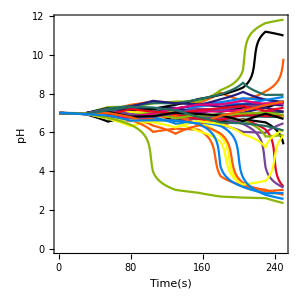

```mathematica
ListPlot[Flatten[Table[dataC⟦i,j,All,1⟧,{i,1,6},{j,1,6}],1],PlotRange-> Full,AspectRatio->1,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotStyle->ColorData[3,"ColorList"],Frame->True,FrameLabel->{"Time(s)","pH"},Joined-> True,ImageSize->300]
```

```mathematica
plotpH[t_]:=Graphics[Flatten@Table[{state3[dataC⟦i,j,10t,1⟧],Disk[{2i,2j},0.45](* Rectangle[{2i-0.45,2j-0.45},{2i+0.45,2j+0.45}] *),Black,Circle[{2i,2j},0.9]},{i,nEl},{j,nEl}],ImageSize->300,Frame-> True,FrameTicks-> None,PlotLabel->Text[Style["pH Distribution",FontSize->14,FontColor->Black]]]
```

```mathematica
plot[nEl_,t_]:=GraphicsRow[{plotVoltage[nEl,t],Show[{plotCurrentCon[nEl,t],plotCurrent[nEl,t],plotCurrentVec[nEl,t,Red]},Frame-> True,FrameTicks-> None],plotpH[t]},Frame-> All,PlotLabel->Text[Style["Time:"<>ToString[t],FontSize->14,FontColor->Black]],ImageSize->600]
```

```mathematica
Export[baseDirectory<>"ElectrodeArray_CV_pH.png",plot[nEl,18],ImageResolution->300]
```

/Users/abhisheksharma/Desktop/Hybrid_Computation_Final/ElectrodeArray_CV_pH.png

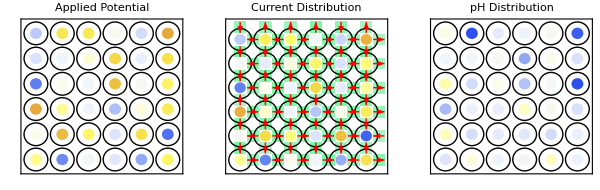

```mathematica
plot[nEl,18]
```

```mathematica
(* data=Table[plot[nEl,k],{k,1,25,0.1}]; *) (* Uncomment to make a gif *)
```

```mathematica
(* Export[baseDirectory<>"ElectrodeArray_CV_pH_2.gif",data] *) (* Uncomment to make a gif *)
```

In this section, we create electrode logic operations without the feedback from the chemical information processing.

```mathematica
Clear[λ,tS,data]
```

```mathematica
offSet=0.5;λ=10^-4;vInit=0.0;tS=2.5; (* Initial potential at time step 1 *)
```

```mathematica
electroChemAutomata[N_,nTs_,potPatterns_]:=Module[{eqLen1,eqLen2,params,params2i,params2f,params3,cnTs,params4,ic,eqnsF,varsEq,eqnsFF,state,state2,currentEL,dataPlot},
eqLen1=Total@{Length[Union@Flatten@eqns[N,tS]⟦All,1⟧],Length[Union@Flatten@eqnsCon[N]⟦All,1⟧],Length[Union@dropletEndConnections2D[N]⟦1⟧]};
eqLen2=Total@{Length[Union@Flatten@eqns[N,tS]⟦All,2⟧],Length[Union@Flatten@eqnsCon[N]⟦All,2⟧],Length[Union@dropletEndConnections2D[N]⟦2⟧]};
(* Checking Number of Equations and Variables *)
Print[eqLen1== eqLen2];
Print["No. of variables ", eqLen2];
params={AreaEL->UnitConvert[π elecRadius^2],RBulkA->dropletBulkR0,RBulkB->dropletBulkR,RConn->dropletBulkInt,i0->ExCurrentDensity,iL->iLim,αa-> 0.5,αc-> 0.5,Cdl-> CDL,E0-> 0}/.q_Quantity:>QuantityMagnitude[q];
Print[params];
cnTs=0;Vapp={}; solnS={}; 
While[cnTs≤ nTs,
Clear[eqnsF,varsEq];
Print["Current Switching Step: ", cnTs];
If[cnTs==0,
params2i=Table[(Symbol["Vi"<>ToString[i]<>"s"<>ToString[j]]->0.0),{i,1,N},{j,1,N}]//Flatten;
params2f=Table[(Symbol["Vf"<>ToString[i]<>"s"<>ToString[j]]->vInit),{i,1,N},{j,1,N}]//Flatten ;
Vapp=Join[Vapp,{{params2i⟦All,2⟧,params2f⟦All,2⟧}}];,

params2i=MapThread[#1-> #2&,{Flatten[Table[Symbol["Vi"<>ToString[i]<>"s"<>ToString[j]],{i,1,N},{j,1,N}]],Vapp⟦cnTs⟧⟦2⟧}];
params2f=Table[(Symbol["Vf"<>ToString[i]<>"s"<>ToString[j]]->potPatterns⟦i,j⟧),{i,1,N},{j,1,N}]//Flatten;
Vapp=Join[Vapp,{{params2i⟦All,2⟧,params2f⟦All,2⟧}}];];

(* Setting up equations *)
eqnsF[N]:=Flatten[{eqns[N,cnTs tS+offSet]⟦All,1⟧,eqnsCon[N]⟦All,1⟧,eqnsEndCon[N]⟦1⟧}];
varsEq[N]:=Flatten[{eqns[N,cnTs tS+offSet]⟦All,2⟧,eqnsCon[N]⟦All,2⟧,eqnsEndCon[N]⟦2⟧}];

(* Setting up initial conditions from previous electrode switching step *)
If[cnTs== 0,
ic[N]:=Flatten@{#== 0&/@Evaluate[varsEq[N]/.t-> cnTs tS]},
ic[N]:=MapThread[{#1==#2}&,{Evaluate[varsEq[N]/.t->cnTs tS],Evaluate[Evaluate[varsEq[N]/.solnS⟦cnTs⟧]/.t->cnTs tS]}];];

eqnsFF=Flatten@{eqnsF[N]/.params/.params2i/.params2f/.q_Quantity:>QuantityMagnitude[q],ic[N]};
Monitor[soln=NDSolve[eqnsFF,varsEq[N],{t,tS cnTs, tS (cnTs+1)},MaxSteps->10^4,MaxStepSize->0.1,Method->Automatic,EvaluationMonitor:>(step=t)],step];
solnS=Join[solnS,soln];cnTs=cnTs+1;]];
```

```mathematica
vInit=1. 10^-12;
```

```mathematica
nEl=5; (* Number of electrodes along X and Y *)
```

```mathematica
potPatterns=Table[vInit,{i,nEl},{j,nEl}];
```

```mathematica
potPatterns⟦Quotient[nEl,2]+1,Quotient[nEl,2]+1⟧=2.5;potPatterns⟦Quotient[nEl,2],Quotient[nEl,2]+1⟧=-2.5;potPatterns⟦Quotient[nEl,2]+2,Quotient[nEl,2]+1⟧=-2.5;potPatterns⟦Quotient[nEl,2]+1,Quotient[nEl,2]⟧=-2.5;potPatterns⟦Quotient[nEl,2]+1,Quotient[nEl,2]+2⟧=-2.5;
potPatterns//MatrixForm
```

(1.×10^-12 | 1.×10^-12 | 1.×10^-12 | 1.×10^-12 | 1.×10^-12
1.×10^-12 | 1.×10^-12 | -2.5 | 1.×10^-12 | 1.×10^-12
1.×10^-12 | -2.5 | 2.5 | -2.5 | 1.×10^-12
1.×10^-12 | 1.×10^-12 | -2.5 | 1.×10^-12 | 1.×10^-12
1.×10^-12 | 1.×10^-12 | 1.×10^-12 | 1.×10^-12 | 1.×10^-12)

```mathematica
electroChemAutomata[nEl,1,potPatterns]
```

True

No. of variables 335

{AreaEL→3.14159×10^-6,RBulkA→423.592,RBulkB→665.377,RConn→665.377,i0→24.1213,iL→9.64853,αa→0.5,αc→0.5,Cdl→0.2,E0→0}

Current Switching Step: 0

Current Switching Step: 1

```mathematica
Clear[dataC]
```

```mathematica
cA=icAM;cB=icBM;cC=icCM;cD=icDM;
```

```mathematica
Block[{currentData,dim},
(* Calculating Current Data for pH estimation *)
currentData=Table[Block[{currentEL,cnT,time},cnT=Quotient[tC,tS]+1;time=Mod[tC,tS];currentEL=(Evaluate[Table[(Symbol["iEL"<>ToString[i]<>"s"<>ToString[j]][t]),{i,nEl},{j,nEl}]/.solnS⟦cnT⟧])/.t->tC],{tC,0.01,5,0.1}];
dim=Dimensions[currentData];
Print[dim];
dataC=Table[Block[{dat=currentData⟦All,p,q⟧},
cA=icAM;cB=icBM;cC=icCM;cD=icDM;Quiet[Monitor[Table[Block[{out},out=pHdropletUpdate[dat⟦i⟧,0.1,{cA,cB,cC,cD}];cA=out⟦2⟧;cB=out⟦3⟧;cC=out⟦4⟧;cD=out⟦5⟧;
out],{i,1,Length[dat]}],i]]],{p,1,dim⟦2⟧},{q,1,dim⟦3⟧}];]
```

{50,5,5}

```mathematica
Dimensions[dataC]
```

{5,5,50,5}

```mathematica
timePoints=Table[t,{t,0.1,4,0.1}];
```

```mathematica
plotVoltageX[nEl_,tC_]:=Block[{plotV,cnT,time},
cnT=Quotient[tC,tS]+1;
time=Mod[tC,tS];
plotV=Partition[Table[fVShift[{Vapp⟦cnT,1,i⟧,Vapp⟦cnT,2,i⟧},{λ,offSet},time],{i,nEl^2}],nEl]];
```

```mathematica
dat=Table[plotVoltageX[nEl,t],{t,0.1,4,0.1}];
```

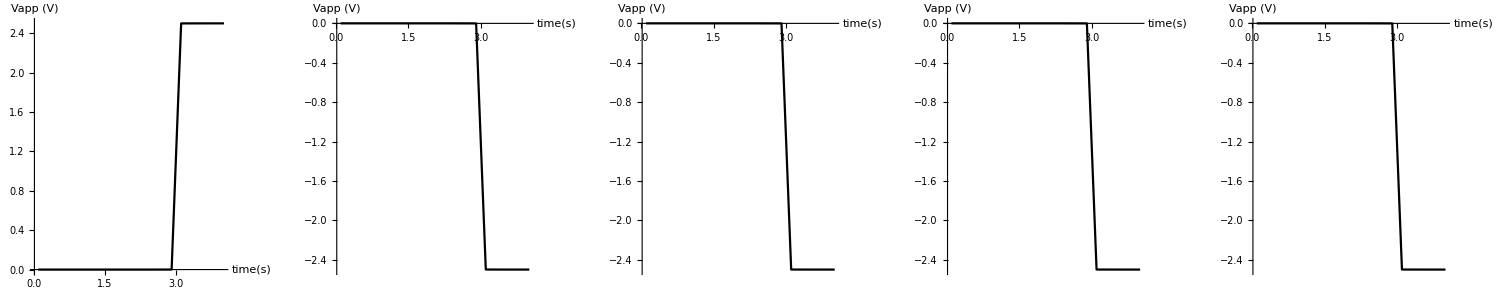

```mathematica
GraphicsRow[{ListPlot[MapThread[{#1,#2}&,{timePoints,dat[[All,3,3]]}],Joined->True,PlotStyle->Black,PlotRange-> Full,PlotStyle->Black,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},AxesLabel->{"time(s)","Vapp (V)"}],
ListPlot[MapThread[{#1,#2}&,{timePoints,dat[[All,2,3]]}],Joined->True,PlotStyle->Black,PlotRange-> Full,PlotStyle->Black,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},AxesLabel->{"time(s)","Vapp (V)"}],
ListPlot[MapThread[{#1,#2}&,{timePoints,dat[[All,4,3]]}],Joined->True,PlotStyle->Black,PlotRange-> Full,PlotStyle->Black,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},AxesLabel->{"time(s)","Vapp (V)"}],
ListPlot[MapThread[{#1,#2}&,{timePoints,dat[[All,3,2]]}],Joined->True,PlotStyle->Black,PlotRange-> Full,PlotStyle->Black,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},AxesLabel->{"time(s)","Vapp (V)"}],ListPlot[MapThread[{#1,#2}&,{timePoints,dat[[All,3,4]]}],Joined->True,PlotStyle->Black,PlotRange-> Full,PlotStyle->Black,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},AxesLabel->{"time(s)","Vapp (V)"}]},ImageSize->1500]
```

```mathematica
plotCurrentX[nEl_,tC_]:=Block[{currentEL,cnT,time},
cnT=Quotient[tC,tS]+1;
time=Mod[tC,tS];
currentEL=(Evaluate[Table[(Symbol["iEL"<>ToString[i]<>"s"<>ToString[j]][t]),{i,nEl},{j,nEl}]/.solnS⟦cnT⟧])/.t->tC]
```

```mathematica
dat=Table[10^3 plotCurrentX[nEl,time],{time,0.1,4,0.1}];
```

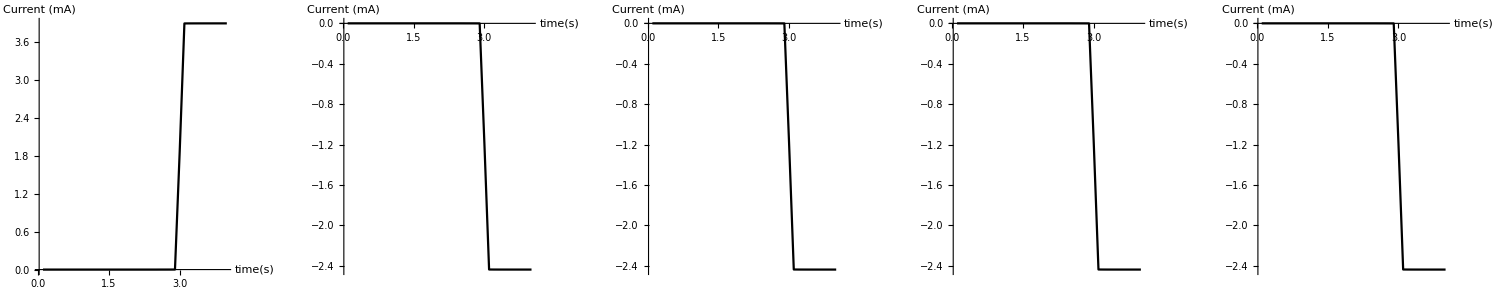

```mathematica
GraphicsRow[{ListPlot[MapThread[{#1,#2}&,{timePoints,dat[[All,3,3]]}],Joined->True,PlotStyle->Black,PlotRange-> Full,PlotStyle->Black,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},AxesLabel->{"time(s)","Current (mA)"}],
ListPlot[MapThread[{#1,#2}&,{timePoints,dat[[All,2,3]]}],Joined->True,PlotStyle->Black,PlotRange-> Full,PlotStyle->Black,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},AxesLabel->{"time(s)","Current (mA)"}],
ListPlot[MapThread[{#1,#2}&,{timePoints,dat[[All,4,3]]}],Joined->True,PlotStyle->Black,PlotRange-> Full,PlotStyle->Black,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},AxesLabel->{"time(s)","Current (mA)"}],
ListPlot[MapThread[{#1,#2}&,{timePoints,dat[[All,3,2]]}],Joined->True,PlotStyle->Black,PlotRange-> Full,PlotStyle->Black,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},AxesLabel->{"time(s)","Current (mA)"}],ListPlot[MapThread[{#1,#2}&,{timePoints,dat[[All,3,4]]}],Joined->True,PlotStyle->Black,PlotRange-> Full,PlotStyle->Black,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},AxesLabel->{"time(s)","Current (mA)"}]},ImageSize->1500]
```

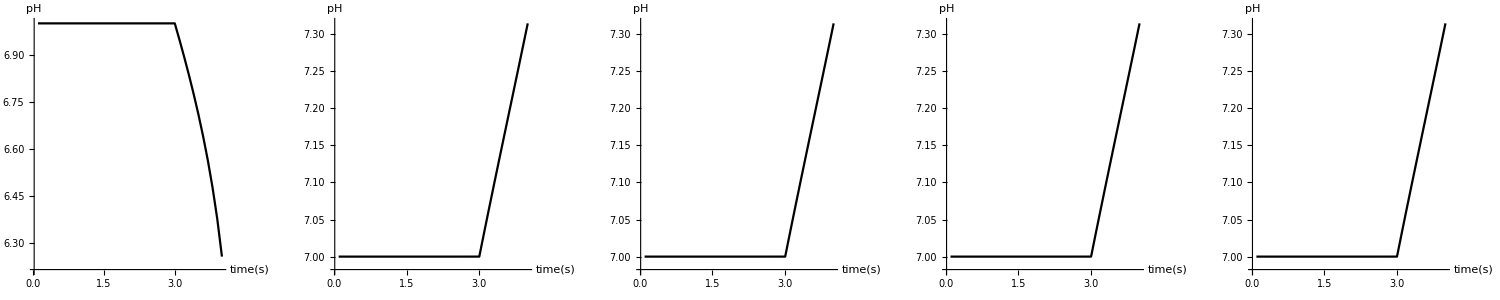

```mathematica
GraphicsRow[{ListPlot[MapThread[{#1,#2}&,{timePoints,dataC⟦3,3,All,1⟧[[1;;Length@timePoints]]}],Joined->True,PlotStyle->Black,PlotRange-> Full,PlotStyle->Black,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},AxesLabel->{"time(s)","pH"}],
ListPlot[MapThread[{#1,#2}&,{timePoints,dataC⟦2,3,All,1⟧[[1;;Length@timePoints]]}],Joined->True,PlotStyle->Black,PlotRange-> Full,PlotStyle->Black,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},AxesLabel->{"time(s)","pH"}],
ListPlot[MapThread[{#1,#2}&,{timePoints,dataC⟦4,3,All,1⟧[[1;;Length@timePoints]]}],Joined->True,PlotStyle->Black,PlotRange-> Full,PlotStyle->Black,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},AxesLabel->{"time(s)","pH"}],ListPlot[MapThread[{#1,#2}&,{timePoints,dataC⟦3,2,All,1⟧[[1;;Length@timePoints]]}],Joined->True,PlotStyle->Black,PlotRange-> Full,PlotStyle->Black,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},AxesLabel->{"time(s)","pH"}],ListPlot[MapThread[{#1,#2}&,{timePoints,dataC⟦3,4,All,1⟧[[1;;Length@timePoints]]}],Joined->True,PlotStyle->Black,PlotRange-> Full,PlotStyle->Black,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},AxesLabel->{"time(s)","pH"}]},ImageSize->1500]
```

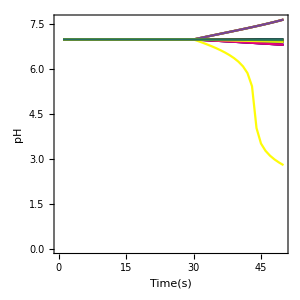

```mathematica
ListPlot[Flatten[Table[dataC⟦i,j,All,1⟧,{i,1,5},{j,1,5}],1],PlotRange-> Full,Joined-> True,PlotStyle->ColorData[3,"ColorList"],AspectRatio->1,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},Frame->True,FrameLabel->{"Time(s)","pH"},ImageSize->300]
```

```mathematica
stateV[k_]:=ColorData[{"TemperatureMap",{-2.5,2.5}}][k]; (* Applied Potential *)
state1[k_]:=ColorData[{"TemperatureMap",{-1.0 10^-3,1.0 10^-3}}][k]; (* Electrode Current *)
state2[k_]:=ColorData[{"MintColors",{0,1 10^-3}}][k]; (* Interfacial Current *)
state3[k_]:=ColorData[{"TemperatureMap",{4,11}}][k]; (* pH profile *)
```

```mathematica
plotpH[t_]:=Graphics[Flatten@Table[{state3[dataC⟦i,j,10t,1⟧],Disk[{2i,2j},0.45](* Rectangle[{2i-0.45,2j-0.45},{2i+0.45,2j+0.45}] *),Black,Circle[{2i,2j},0.9]},{i,nEl},{j,nEl}],ImageSize->300,Frame-> True,FrameTicks-> None,PlotLabel->Text[Style["pH Distribution",FontSize->14,FontColor->Black]]]
```

```mathematica
plot[nEl_,t_]:=GraphicsRow[{plotVoltage[nEl,t],Show[{plotCurrentCon[nEl,t],plotCurrent[nEl,t],plotCurrentVec[nEl,t,Red]},Frame-> True,FrameTicks-> None,ImageSize->300],plotpH[t]},Frame-> All,PlotLabel->Text[Style["Time:"<>ToString[t],FontSize->14,FontColor->Black]]]
```

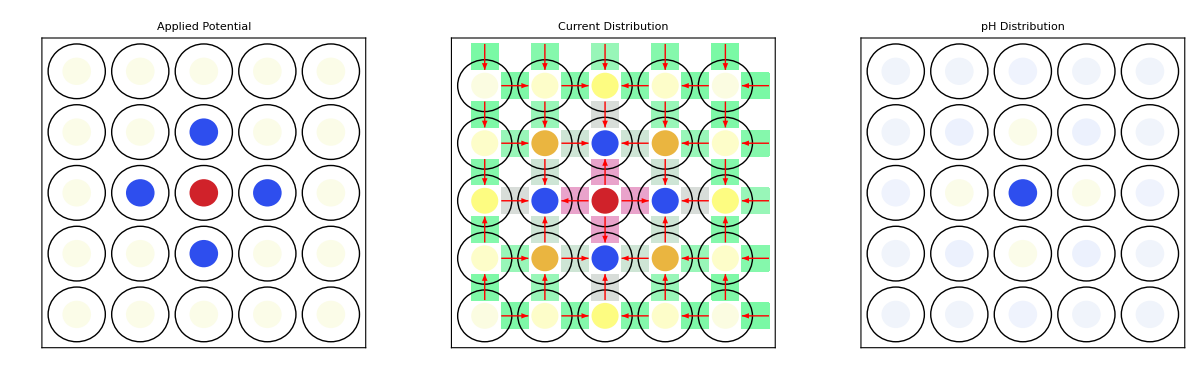

```mathematica
plot[nEl,4.5]
```

```mathematica
nEl=5; (* Number of electrodes along X and Y *)
```

```mathematica
potPatterns=Table[vInit,{i,nEl},{j,nEl}];
```

```mathematica
potPatterns⟦Quotient[nEl,2]+1,Quotient[nEl,2]+1⟧=-2.5;potPatterns⟦Quotient[nEl,2],Quotient[nEl,2]+1⟧=2.5;potPatterns⟦Quotient[nEl,2]+2,Quotient[nEl,2]+1⟧=2.5;potPatterns⟦Quotient[nEl,2]+1,Quotient[nEl,2]⟧=2.5;potPatterns⟦Quotient[nEl,2]+1,Quotient[nEl,2]+2⟧=2.5;
potPatterns//MatrixForm
```

(1.×10^-12 | 1.×10^-12 | 1.×10^-12 | 1.×10^-12 | 1.×10^-12
1.×10^-12 | 1.×10^-12 | 2.5 | 1.×10^-12 | 1.×10^-12
1.×10^-12 | 2.5 | -2.5 | 2.5 | 1.×10^-12
1.×10^-12 | 1.×10^-12 | 2.5 | 1.×10^-12 | 1.×10^-12
1.×10^-12 | 1.×10^-12 | 1.×10^-12 | 1.×10^-12 | 1.×10^-12)

```mathematica
electroChemAutomata[nEl,1,potPatterns]
```

True

No. of variables 335

{AreaEL→3.14159×10^-6,RBulkA→423.592,RBulkB→665.377,RConn→665.377,i0→24.1213,iL→9.64853,αa→0.5,αc→0.5,Cdl→0.2,E0→0}

Current Switching Step: 0

Current Switching Step: 1

```mathematica
Clear[dataC]
```

```mathematica
cA=icAM;cB=icBM;cC=icCM;cD=icDM;
```

```mathematica
Block[{currentData,dim},
(* Calculating Current Data for pH estimation *)
currentData=Table[Block[{currentEL,cnT,time},cnT=Quotient[tC,tS]+1;time=Mod[tC,tS];currentEL=(Evaluate[Table[(Symbol["iEL"<>ToString[i]<>"s"<>ToString[j]][t]),{i,nEl},{j,nEl}]/.solnS⟦cnT⟧])/.t->tC],{tC,0.01,5,0.1}];
dim=Dimensions[currentData];
Print[dim];
dataC=Table[Block[{dat=currentData⟦All,p,q⟧},
cA=icAM;cB=icBM;cC=icCM;cD=icDM;Quiet[Monitor[Table[Block[{out},out=pHdropletUpdate[dat⟦i⟧,0.1,{cA,cB,cC,cD}];cA=out⟦2⟧;cB=out⟦3⟧;cC=out⟦4⟧;cD=out⟦5⟧;
out],{i,1,Length[dat]}],i]]],{p,1,dim⟦2⟧},{q,1,dim⟦3⟧}];]
```

{50,5,5}

```mathematica
Dimensions[dataC]
```

{5,5,50,5}

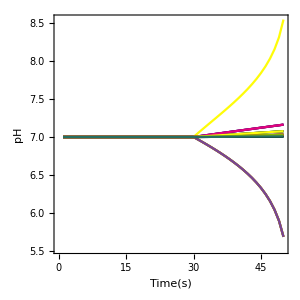

```mathematica
ListPlot[Flatten[Table[dataC⟦i,j,All,1⟧,{i,1,5},{j,1,5}],1],PlotRange-> Full,Joined-> True,AspectRatio->1,PlotStyle->ColorData[3,"ColorList"],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},Frame->True,FrameLabel->{"Time(s)","pH"},ImageSize->300]
```

## Programmable pH changes with proportional logic : Single Working Electrode

In this section, we program pH changes over an electroactive arrays using proportional logic, with different control parameters. In this case, we will start with a minimalistic set of electrode arrays, and try to set different pHs over the electrodes.

```mathematica
Clear[λ,tS,data]
```

```mathematica
offSet=0.25; (* Electrode Potential offset time for shifting *)
λ=10^-4; (* Parameter for sharpness of potential shift *)
tS=1.5; (* Time step for potential shift in seconds *) 
vInit = 1 10^-6; (* Potential on inactive electrode in absense of applied potential for numerical stability *)
timeStep = 0.1; (* Time stepping for pH calculation in seconds *)
switchTime=60.0;(* Switch time between two pH states on the working electrode *)
αVoltage=0.25; (* Proportional factor for applied voltage based on pH difference *)
potPatterns=Table[vInit,{i,nEl},{j,nEl}]; (* Initial potential patterns *)
```

```mathematica
nEl=5; (* Number of electrodes along X and Y *)
```

```mathematica
nEl=5; (* Number of electrodes along X and Y *)
nElW =1; (* Number of working electrodes along X ans Y *)
```

```mathematica
{icAM,icBM,icCM,icDM} (* Initial concentration of phosphate species in each droplet *)
```

{3.45607×10^-8,0.00773718,0.0122626,1.73214×10^-7}

```mathematica
(* Defining concentration of phosphate species on each droplet *)
cAdroplet=Table[icAM,{i,nEl},{j,nEl}]; 
cBdroplet=Table[icBM,{i,nEl},{j,nEl}]; 
cCdroplet=Table[icCM,{i,nEl},{j,nEl}];cDdroplet=Table[icDM,{i,nEl},{j,nEl}];
```

```mathematica
Clear[dataT];dataT= {};pHdiffRec={}; (* Empty array for storing pH values *)
```

```mathematica
(* Initializing all electrodes as INACTIVE *)
Clear[electrodeType]
electrodeType=Table["INACTIVE",{i,nEl},{j,nEl}];
```

```mathematica
WE={{3,3}};
```

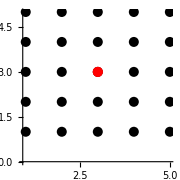

```mathematica
Show[{ListPlot[Flatten[Table[{i,j},{i,nEl},{j,nEl}],1],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},PlotStyle->{Black,PointSize-> 0.04},Frame-> None,FrameTicks->None,AspectRatio->1],ListPlot[WE,PlotStyle->{Red,PointSize-> 0.04},Frame-> None,FrameTicks->None,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},AspectRatio->1]},ImageSize-> Small]
```

```mathematica
(electrodeType⟦WE⟦#,1⟧,WE⟦#,2⟧⟧="ACTIVE")&/@Range[Length[WE]];
```

```mathematica
(* Activating neighbouring Counter Electrodes *)
```

```mathematica
CE=Union[Flatten[Block[{elec=WE⟦#⟧},{{elec⟦1⟧+1,elec⟦2⟧},{elec⟦1⟧,elec⟦2⟧+1},{elec⟦1⟧-1,elec⟦2⟧},{elec⟦1⟧,elec⟦2⟧-1}}]&/@Range[Length[WE]],1]];
```

Checking if WE and CE are correct.

```mathematica
{WE,CE}
```

{{{3,3}},{{2,3},{3,2},{3,4},{4,3}}}

```mathematica
(electrodeType⟦CE⟦#,1⟧,CE⟦#,2⟧⟧="ACTIVE")&/@Range[Length[CE]];
```

```mathematica
electrodeType//MatrixForm
```

(INACTIVE | INACTIVE | INACTIVE | INACTIVE | INACTIVE
INACTIVE | INACTIVE | ACTIVE | INACTIVE | INACTIVE
INACTIVE | ACTIVE | ACTIVE | ACTIVE | INACTIVE
INACTIVE | INACTIVE | ACTIVE | INACTIVE | INACTIVE
INACTIVE | INACTIVE | INACTIVE | INACTIVE | INACTIVE)

```mathematica
(* Initializing potentials on all the electrodes*)
```

```mathematica
(* Finding neighbouring working electrodes around each counter electrode *)
```

```mathematica
NeighboursWE[ce_]:=Block[{eX=ce⟦1⟧,eY=ce⟦2⟧},{{eX+1,eY},{eX,eY+1},{eX-1,eY},{eX,eY-1}}]
```

```mathematica
neighbourlistWE=Table[Select[NeighboursWE[CE⟦i⟧],MemberQ[WE,#]&],{i,Length[CE]}];
```

For each counter electrode there is only one working electrode.

```mathematica
neighbourlistWE
```

{{{3,3}},{{3,3}},{{3,3}},{{3,3}}}

```mathematica
(* Complete function to electrochemical automata of the droplet array *)
electroChemAutomata[N_,nTs_,setpH_,αVoltage_,tS_]:=Module[{eqLen1,eqLen2,params,params2i,params2f,params3,cnTs,params4,ic,eqnsF,varsEq,eqnsFF,state,state2,currentEL,dataT,Vapp,solnS,dataPlot,dataC,soln,cAdropletC,cBdropletC,cCdropletC,cDdropletC,initStates,initpH,currentpH,setpHe,pHdiff,cePotentials},
eqLen1=Total@{Length[Union@Flatten@eqns[N,tS]⟦All,1⟧],Length[Union@Flatten@eqnsCon[N]⟦All,1⟧],Length[Union@dropletEndConnections2D[N]⟦1⟧]};
eqLen2=Total@{Length[Union@Flatten@eqns[N,tS]⟦All,2⟧],Length[Union@Flatten@eqnsCon[N]⟦All,2⟧],Length[Union@dropletEndConnections2D[N]⟦2⟧]};
(* Checking Number of Equations and Variables *)
PrintTemporary[eqLen1== eqLen2];
PrintTemporary["No. of variables ", eqLen2];
params={AreaEL-> UnitConvert[π elecRadius^2],RBulkA->dropletBulkR0,RBulkB->dropletBulkR,RConn->dropletBulkInt,i0->ExCurrentDensity,iL->iLim,αa-> 0.5,αc-> 0.5,Cdl->CDL,E0-> 0}/.q_Quantity:>QuantityMagnitude[q];
Clear[dim,pHdiffRec];
cnTs=0;Vapp={}; solnS={}; dataT={};pHdiffRec={};
(* Initializing Concentrations of Phosphate species*)
cAdropletC=cAdroplet;
cBdropletC=cBdroplet;
cCdropletC=cCdroplet;
cDdropletC=cDdroplet;
setpHe=setpH; (* Setting the pH on the working electrode to be attained *)

While[cnTs≤ nTs,
Clear[eqnsF,varsEq];
PrintTemporary["-------------------------------------------------------------"];
PrintTemporary["Current Switching Step : ", cnTs, "; Current Time : ", cnTs tS];
(*
If[Mod[Quotient[cnTs tS,switchTime],2] ≠  Mod[Quotient[(cnTs-1) tS,switchTime],2],PrintTemporary["****** SWITCHING TO NEW STATES ******"]];
PrintTemporary["Current pH states : ", setpHe];
*)
Which[cnTs== 0 ,
(* Set initial potential on all the electrodes at t=0 *)
params2i=Table[(Symbol["Vi"<>ToString[i]<>"s"<>ToString[j]]-> 0.),{i,1,N},{j,1,N}]//Flatten;
params2f=Table[(Symbol["Vf"<>ToString[i]<>"s"<>ToString[j]]->vInit),{i,1,N},{j,1,N}]//Flatten ;
Vapp=Join[Vapp,{{params2i⟦All,2⟧,params2f⟦All,2⟧}}],

cnTs≠ 0 ,
(* At any other time step *)
(* Setting potentials on working electrodes, proportional to pH difference *)
(potPatterns⟦WE⟦#,1⟧,WE⟦#,2⟧⟧=-αVoltage pHdiff⟦#⟧)&/@Range[Length[WE]];

(* Setting counter electrode potentials based on neighbouring working electrodes *)
cePotentials=Table[Mean[potPatterns⟦#⟦1⟧,#⟦2⟧⟧&/@neighbourlistWE⟦i⟧],{i,Length[neighbourlistWE]}];
(potPatterns⟦CE⟦#,1⟧,CE⟦#,2⟧⟧=-cePotentials⟦#⟧)&/@Range[Length[CE]];

PrintTemporary["Applying Voltages:"];
PrintTemporary[1.potPatterns//MatrixForm];

params2i=MapThread[#1-> #2&,{Flatten[Table[Symbol["Vi"<>ToString[i]<>"s"<>ToString[j]],{i,1,N},{j,1,N}]],Vapp⟦cnTs⟧⟦2⟧}];
params2f=Table[(Symbol["Vf"<>ToString[i]<>"s"<>ToString[j]]->potPatterns⟦i,j⟧),{i,1,N},{j,1,N}]//Flatten;
Vapp=Join[Vapp,{{params2i⟦All,2⟧,params2f⟦All,2⟧}}]];

(* Setting up equations *)
eqnsF[N]:=Flatten[{eqns[N,cnTs tS+offSet]⟦All,1⟧,eqnsCon[N]⟦All,1⟧,eqnsEndCon[N]⟦1⟧}];
varsEq[N]:=Flatten[{eqns[N,cnTs tS+offSet]⟦All,2⟧,eqnsCon[N]⟦All,2⟧,eqnsEndCon[N]⟦2⟧}];

(* Setting up initial conditions from previous electrode switching step *)
If[cnTs== 0,
ic[N]:=Flatten@{#== 0&/@Evaluate[varsEq[N]/.t-> cnTs tS]},
ic[N]:=MapThread[{#1==#2}&,{Evaluate[varsEq[N]/.t->cnTs tS],Evaluate[Evaluate[varsEq[N]/.solnS⟦cnTs⟧]/.t->cnTs tS]}];];

eqnsFF=Flatten@{eqnsF[N]/.params/.params2i/.params2f/.q_Quantity:>QuantityMagnitude[q],ic[N]};
Monitor[soln=Quiet[NDSolve[eqnsFF,varsEq[N],{t,tS cnTs, tS (cnTs+1)},MaxSteps->10^5,MaxStepSize->0.1,Method->Automatic,EvaluationMonitor:>(step=t)]],step];
solnS=Join[solnS,soln];

(* Updating pH on each droplet *)
currentEL=Flatten[Table[Evaluate[Table[(Symbol["iEL"<>ToString[i]<>"s"<>ToString[j]][t]),{i,nEl},{j,nEl}]/.soln]/.t-> tC,{tC,tS cnTs, tS (cnTs+1),timeStep}],1];

dim=Dimensions[currentEL]; 
PrintTemporary["Dimensions currentEL: ",dim];
(* Initial State on working electrode at step [i] should be equal to the final state of step [i-1] *)
(* Print["Initial State:",(dataC⟦WE⟦#,1⟧,WE⟦#,2⟧,tS/timeStep+1⟧)&/@Range[Length[WE]]]; *)
dataC=ParallelTable[Block[{dat=currentEL⟦All,p,q⟧},
Quiet[Monitor[Table[Block[{out},
out=pHdropletUpdate[dat⟦i⟧,timeStep,{cAdropletC⟦p,q⟧,cBdropletC⟦p,q⟧,cCdropletC⟦p,q⟧,cDdropletC⟦p,q⟧}];
cAdropletC⟦p,q⟧=out⟦2⟧;
cBdropletC⟦p,q⟧=out⟦3⟧;
cCdropletC⟦p,q⟧=out⟦4⟧;
cDdropletC⟦p,q⟧=out⟦5⟧;
out],{i,1,Length[dat]}],i]]],{p,1,dim⟦2⟧},{q,1,dim⟦3⟧}];
PrintTemporary["Dimensions pH data: ", Dimensions@dataC];
(* Print["Final State:",(dataC⟦WE⟦#,1⟧,WE⟦#,2⟧,tS/timeStep+1⟧)&/@Range[Length[WE]]]; *)
currentpH=(dataC⟦WE⟦#,1⟧,WE⟦#,2⟧,tS/timeStep+1⟧⟦1⟧)&/@Range[Length[WE]];
pHdiff=(setpHe-currentpH);

pHdiffRec=Join[pHdiffRec,{pHdiff}];
dataT=Join[dataT,{dataC}];
PrintTemporary["Current Measured pHs : ",NumberForm[currentpH,3]];
PrintTemporary["Current pH differences : ",NumberForm[pHdiff,3]];
cnTs=cnTs+1];
Return[{Vapp,solnS,dataT}]];
```

```mathematica
cnTs=0;nSteps=50;
out1=electroChemAutomata[nEl,nSteps,4,0.1,1.0];
out2=electroChemAutomata[nEl,nSteps,4,0.2,1.0];
out3=electroChemAutomata[nEl,nSteps,4,0.3,1.0];
out4=electroChemAutomata[nEl,nSteps,4,0.4,1.0];
out5=electroChemAutomata[nEl,nSteps,4,0.5,1.0];
```

```mathematica
tS=1.0;
```

```mathematica
timeList=Flatten@Table[Table[tC,{tC,tS cnTs, tS (cnTs+1),timeStep}],{cnTs,0,nSteps}];
```

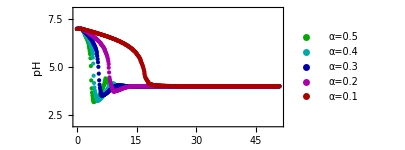

```mathematica
p11=ListPlot[Evaluate[{
Flatten[Table[MapThread[{#1,#2}&,{timeList,Flatten[(out5[[3]]⟦All,WE⟦#,1⟧,WE⟦#,2⟧⟧&/@Range[Length[WE]])⟦i⟧,1]⟦All,1⟧}],{i,1,Length@WE}],1],
Flatten[Table[MapThread[{#1,#2}&,{timeList,Flatten[(out4[[3]]⟦All,WE⟦#,1⟧,WE⟦#,2⟧⟧&/@Range[Length[WE]])⟦i⟧,1]⟦All,1⟧}],{i,1,Length@WE}],1],Flatten[Table[MapThread[{#1,#2}&,{timeList,Flatten[(out3[[3]]⟦All,WE⟦#,1⟧,WE⟦#,2⟧⟧&/@Range[Length[WE]])⟦i⟧,1]⟦All,1⟧}],{i,1,Length@WE}],1],Flatten[Table[MapThread[{#1,#2}&,{timeList,Flatten[(out2[[3]]⟦All,WE⟦#,1⟧,WE⟦#,2⟧⟧&/@Range[Length[WE]])⟦i⟧,1]⟦All,1⟧}],{i,1,Length@WE}],1],Flatten[Table[MapThread[{#1,#2}&,{timeList,Flatten[(out1[[3]]⟦All,WE⟦#,1⟧,WE⟦#,2⟧⟧&/@Range[Length[WE]])⟦i⟧,1]⟦All,1⟧}],{i,1,Length@WE}],1]}],
AspectRatio->0.5,Frame-> True,FrameLabel-> {"Time (s)","pH"},PlotRange-> {All,{2,8}},
LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotStyle->Evaluate[{#,PointSize[0.01]}&/@{Darker@Green,Darker@Cyan,Darker@Blue,Darker@Magenta,Darker@Red}],PlotLegends-> Placed[LineLegend[{"α=0.5", "α=0.4","α=0.3", "α=0.2","α=0.1"},Spacings-> {0.1,0.1}],{0.85,0.65}],ImageSize->300]
```

```mathematica
cnTs=0;nSteps=50;
out1=electroChemAutomata[nEl,nSteps,4,0.1,2.5];
out2=electroChemAutomata[nEl,nSteps,4,0.2,2.5];
out3=electroChemAutomata[nEl,nSteps,4,0.3,2.5];
out4=electroChemAutomata[nEl,nSteps,4,0.4,2.5];
out5=electroChemAutomata[nEl,nSteps,4,0.5,2.5];
```

```mathematica
tS=2.5;
```

```mathematica
timeList=Flatten@Table[Table[tC,{tC,tS cnTs, tS (cnTs+1),timeStep}],{cnTs,0,nSteps}];
```

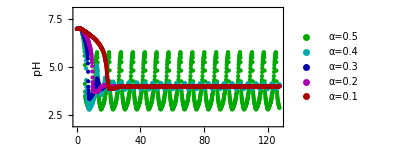

```mathematica
p12=ListPlot[Evaluate[{
Flatten[Table[MapThread[{#1,#2}&,{timeList,Flatten[(out5[[3]]⟦All,WE⟦#,1⟧,WE⟦#,2⟧⟧&/@Range[Length[WE]])⟦i⟧,1]⟦All,1⟧}],{i,1,Length@WE}],1],
Flatten[Table[MapThread[{#1,#2}&,{timeList,Flatten[(out4[[3]]⟦All,WE⟦#,1⟧,WE⟦#,2⟧⟧&/@Range[Length[WE]])⟦i⟧,1]⟦All,1⟧}],{i,1,Length@WE}],1],Flatten[Table[MapThread[{#1,#2}&,{timeList,Flatten[(out3[[3]]⟦All,WE⟦#,1⟧,WE⟦#,2⟧⟧&/@Range[Length[WE]])⟦i⟧,1]⟦All,1⟧}],{i,1,Length@WE}],1],Flatten[Table[MapThread[{#1,#2}&,{timeList,Flatten[(out2[[3]]⟦All,WE⟦#,1⟧,WE⟦#,2⟧⟧&/@Range[Length[WE]])⟦i⟧,1]⟦All,1⟧}],{i,1,Length@WE}],1],Flatten[Table[MapThread[{#1,#2}&,{timeList,Flatten[(out1[[3]]⟦All,WE⟦#,1⟧,WE⟦#,2⟧⟧&/@Range[Length[WE]])⟦i⟧,1]⟦All,1⟧}],{i,1,Length@WE}],1]}],
AspectRatio->0.5,Frame-> True,FrameLabel-> {"Time (s)","pH"},PlotRange-> {All,{2,8}},
LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotStyle->Evaluate[{#,PointSize[0.01]}&/@{Darker@Green,Darker@Cyan,Darker@Blue,Darker@Magenta,Darker@Red}],PlotLegends-> Placed[LineLegend[{"α=0.5", "α=0.4","α=0.3", "α=0.2","α=0.1"},LegendLayout->"Row",Spacings-> {0.1,0.1}],{0.5,0.9}],ImageSize->300]
```

```mathematica
cnTs=0;nSteps=50;
out1=electroChemAutomata[nEl,nSteps,10,0.1,1.0];
out2=electroChemAutomata[nEl,nSteps,10,0.2,1.0];
out3=electroChemAutomata[nEl,nSteps,10,0.3,1.0];
out4=electroChemAutomata[nEl,nSteps,10,0.4,1.0];
out5=electroChemAutomata[nEl,nSteps,10,0.5,1.0];
```

```mathematica
tS=1.0;
```

```mathematica
timeList=Flatten@Table[Table[tC,{tC,tS cnTs, tS (cnTs+1),timeStep}],{cnTs,0,nSteps}];
```

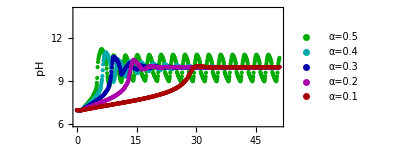

```mathematica
p21=ListPlot[Evaluate[{
Flatten[Table[MapThread[{#1,#2}&,{timeList,Flatten[(out5[[3]]⟦All,WE⟦#,1⟧,WE⟦#,2⟧⟧&/@Range[Length[WE]])⟦i⟧,1]⟦All,1⟧}],{i,1,Length@WE}],1],
Flatten[Table[MapThread[{#1,#2}&,{timeList,Flatten[(out4[[3]]⟦All,WE⟦#,1⟧,WE⟦#,2⟧⟧&/@Range[Length[WE]])⟦i⟧,1]⟦All,1⟧}],{i,1,Length@WE}],1],Flatten[Table[MapThread[{#1,#2}&,{timeList,Flatten[(out3[[3]]⟦All,WE⟦#,1⟧,WE⟦#,2⟧⟧&/@Range[Length[WE]])⟦i⟧,1]⟦All,1⟧}],{i,1,Length@WE}],1],Flatten[Table[MapThread[{#1,#2}&,{timeList,Flatten[(out2[[3]]⟦All,WE⟦#,1⟧,WE⟦#,2⟧⟧&/@Range[Length[WE]])⟦i⟧,1]⟦All,1⟧}],{i,1,Length@WE}],1],Flatten[Table[MapThread[{#1,#2}&,{timeList,Flatten[(out1[[3]]⟦All,WE⟦#,1⟧,WE⟦#,2⟧⟧&/@Range[Length[WE]])⟦i⟧,1]⟦All,1⟧}],{i,1,Length@WE}],1]}],
AspectRatio->0.5,Frame-> True,FrameLabel-> {"Time (s)","pH"},PlotRange-> {All,{6,14}},
LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotStyle->Evaluate[{#,PointSize[0.01]}&/@{Darker@Green,Darker@Cyan,Darker@Blue,Darker@Magenta,Darker@Red}],PlotLegends-> Placed[LineLegend[{"α=0.5", "α=0.4","α=0.3", "α=0.2","α=0.1"},LegendLayout->"Row",Spacings-> {0.1,0.1}],{0.5,0.9}],ImageSize->300]
```

```mathematica
cnTs=0;nSteps=50;
out1=electroChemAutomata[nEl,nSteps,10,0.1,2.5];
out2=electroChemAutomata[nEl,nSteps,10,0.2,2.5];
out3=electroChemAutomata[nEl,nSteps,10,0.3,2.5];
out4=electroChemAutomata[nEl,nSteps,10,0.4,2.5];
out5=electroChemAutomata[nEl,nSteps,10,0.5,2.5];
```

```mathematica
tS=2.5;
```

```mathematica
timeList=Flatten@Table[Table[tC,{tC,tS cnTs, tS (cnTs+1),timeStep}],{cnTs,0,nSteps}];
```

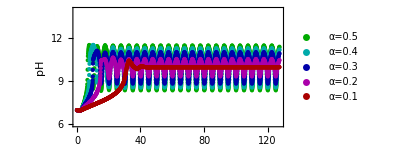

```mathematica
p22=ListPlot[Evaluate[{
Flatten[Table[MapThread[{#1,#2}&,{timeList,Flatten[(out5[[3]]⟦All,WE⟦#,1⟧,WE⟦#,2⟧⟧&/@Range[Length[WE]])⟦i⟧,1]⟦All,1⟧}],{i,1,Length@WE}],1],
Flatten[Table[MapThread[{#1,#2}&,{timeList,Flatten[(out4[[3]]⟦All,WE⟦#,1⟧,WE⟦#,2⟧⟧&/@Range[Length[WE]])⟦i⟧,1]⟦All,1⟧}],{i,1,Length@WE}],1],Flatten[Table[MapThread[{#1,#2}&,{timeList,Flatten[(out3[[3]]⟦All,WE⟦#,1⟧,WE⟦#,2⟧⟧&/@Range[Length[WE]])⟦i⟧,1]⟦All,1⟧}],{i,1,Length@WE}],1],Flatten[Table[MapThread[{#1,#2}&,{timeList,Flatten[(out2[[3]]⟦All,WE⟦#,1⟧,WE⟦#,2⟧⟧&/@Range[Length[WE]])⟦i⟧,1]⟦All,1⟧}],{i,1,Length@WE}],1],Flatten[Table[MapThread[{#1,#2}&,{timeList,Flatten[(out1[[3]]⟦All,WE⟦#,1⟧,WE⟦#,2⟧⟧&/@Range[Length[WE]])⟦i⟧,1]⟦All,1⟧}],{i,1,Length@WE}],1]}],
AspectRatio->0.5,Frame-> True,FrameLabel-> {"Time (s)","pH"},PlotRange-> {All,{6,14}},
LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotStyle->Evaluate[{#,PointSize[0.01]}&/@{Darker@Green,Darker@Cyan,Darker@Blue,Darker@Magenta,Darker@Red}],PlotLegends-> Placed[LineLegend[{"α=0.5", "α=0.4","α=0.3", "α=0.2","α=0.1"},LegendLayout->"Row",Spacings-> {0.1,0.1}],{0.5,0.9}],ImageSize->300]
```

```mathematica
Export[baseDirectory<>"pHControl_1.png",p11,ImageResolution->300]
```

/Users/abhisheksharma/Desktop/Hybrid_Computation_Final/pHControl_1.png

```mathematica
Export[baseDirectory<>"pHControl_2.png",p12,ImageResolution->300]
```

/Users/abhisheksharma/Desktop/Hybrid_Computation_Final/pHControl_2.png

```mathematica
Export[baseDirectory<>"pHControl_3.png",p21,ImageResolution->300]
```

/Users/abhisheksharma/Desktop/Hybrid_Computation_Final/pHControl_3.png

```mathematica
Export[baseDirectory<>"pHControl_4.png",p22,ImageResolution->300]
```

/Users/abhisheksharma/Desktop/Hybrid_Computation_Final/pHControl_4.png

## Programmable pH changes with proportional logic : Multiple Working Electrodes

In this section, we program pH changes over an electroactive arrays using proportional logic, with different control parameters. In this case, we will start with a minimalistic set of electrode arrays, and try to set different pHs over the electrodes.

```mathematica
Clear[λ,tS,data]
```

```mathematica
offSet=0.25; (* Electrode Potential offset time for shifting *)
λ=10^-4; (* Parameter for sharpness of potential shift *)
tS=1.5; (* Time step for potential shift in seconds *) 
vInit = 1 10^-6; (* Potential on inactive electrode in absense of applied potential for numerical stability *)
timeStep = 0.1; (* Time stepping for pH calculation in seconds *)
switchTime=60.0;(* Switch time between two pH states on the working electrode *)
potPatterns=Table[vInit,{i,nEl},{j,nEl}]; (* Initial potential patterns *)
```

```mathematica
nEl=5; (* Number of electrodes along X and Y *)
```

```mathematica
nEl=5; (* Number of electrodes along X and Y *)
nElW =1; (* Number of working electrodes along X ans Y  : This is not the actual number of working electrodes, it is used to create four working electrodes *)
```

```mathematica
{icAM,icBM,icCM,icDM} (* Initial concentration of phosphate species in each droplet *)
```

{3.45607×10^-8,0.00773718,0.0122626,1.73214×10^-7}

```mathematica
(* Defining concentration of phosphate species on each droplet *)
cAdroplet=Table[icAM,{i,nEl},{j,nEl}]; 
cBdroplet=Table[icBM,{i,nEl},{j,nEl}]; 
cCdroplet=Table[icCM,{i,nEl},{j,nEl}];cDdroplet=Table[icDM,{i,nEl},{j,nEl}];
```

```mathematica
Clear[dataT];dataT= {};pHdiffRec={}; (* Empty array for storing pH values *)
```

```mathematica
(* Initializing all electrodes as INACTIVE *)
Clear[electrodeType]
electrodeType=Table["INACTIVE",{i,nEl},{j,nEl}];
```

```mathematica
WE=Flatten[Table[{i,j},{i,Ceiling[nEl/2]-(Ceiling[nElW/2]),Ceiling[nEl/2]+(Ceiling[nElW/2]),2},{j,Ceiling[nEl/2]-(Ceiling[nElW/2]),Ceiling[nEl/2]+(Ceiling[nElW/2]),2}],1]
```

{{2,2},{2,4},{4,2},{4,4}}

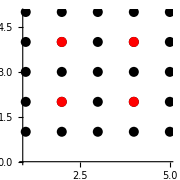

```mathematica
elLayout=Show[{ListPlot[Flatten[Table[{i,j},{i,nEl},{j,nEl}],1],LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},PlotStyle->{Black,PointSize-> 0.04},Frame-> None,FrameTicks->None,AspectRatio->1],ListPlot[WE,PlotStyle->{Red,PointSize-> 0.04},Frame-> None,FrameTicks->None,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->12]},AspectRatio->1]},ImageSize-> Small]
```

```mathematica
Export[baseDirectory<>"electrodeLayout.svg",elLayout]
```

/Users/abhisheksharma/Desktop/Hybrid_Computation_Final/electrodeLayout.svg

```mathematica
(electrodeType⟦WE⟦#,1⟧,WE⟦#,2⟧⟧="ACTIVE")&/@Range[Length[WE]];
```

```mathematica
(* Activating neighbouring Counter Electrodes *)
```

```mathematica
CE=Union[Flatten[Block[{elec=WE⟦#⟧},{{elec⟦1⟧+1,elec⟦2⟧},{elec⟦1⟧,elec⟦2⟧+1},{elec⟦1⟧-1,elec⟦2⟧},{elec⟦1⟧,elec⟦2⟧-1}}]&/@Range[Length[WE]],1]];
```

```mathematica
(electrodeType⟦CE⟦#,1⟧,CE⟦#,2⟧⟧="ACTIVE")&/@Range[Length[CE]];
```

```mathematica
electrodeType//MatrixForm
```

(INACTIVE | ACTIVE | INACTIVE | ACTIVE | INACTIVE
ACTIVE | ACTIVE | ACTIVE | ACTIVE | ACTIVE
INACTIVE | ACTIVE | INACTIVE | ACTIVE | INACTIVE
ACTIVE | ACTIVE | ACTIVE | ACTIVE | ACTIVE
INACTIVE | ACTIVE | INACTIVE | ACTIVE | INACTIVE)

```mathematica
(* Initializing potentials on all the electrodes*)
```

```mathematica
(* Finding neighbouring working electrodes around each counter electrode *)
```

```mathematica
NeighboursWE[ce_]:=Block[{eX=ce⟦1⟧,eY=ce⟦2⟧},{{eX+1,eY},{eX,eY+1},{eX-1,eY},{eX,eY-1}}]
```

```mathematica
neighbourlistWE=Table[Select[NeighboursWE[CE⟦i⟧],MemberQ[WE,#]&],{i,Length[CE]}];
```

```mathematica
neighbourlistWE
```

{{{2,2}},{{2,4}},{{2,2}},{{2,4},{2,2}},{{2,4}},{{4,2},{2,2}},{{4,4},{2,4}},{{4,2}},{{4,4},{4,2}},{{4,4}},{{4,2}},{{4,4}}}

```mathematica
(* Complete function to electrochemical automata of the droplet array *)
electroChemAutomata[N_,nTs_,setpH_,αVoltage_,tS_]:=Module[{eqLen1,eqLen2,params,params2i,params2f,params3,cnTs,params4,ic,eqnsF,varsEq,eqnsFF,state,state2,currentEL,dataT,Vapp,solnS,dataPlot,dataC,soln,cAdropletC,cBdropletC,cCdropletC,cDdropletC,initStates,initpH,currentpH,setpHe,pHdiff,cePotentials},
eqLen1=Total@{Length[Union@Flatten@eqns[N,tS]⟦All,1⟧],Length[Union@Flatten@eqnsCon[N]⟦All,1⟧],Length[Union@dropletEndConnections2D[N]⟦1⟧]};
eqLen2=Total@{Length[Union@Flatten@eqns[N,tS]⟦All,2⟧],Length[Union@Flatten@eqnsCon[N]⟦All,2⟧],Length[Union@dropletEndConnections2D[N]⟦2⟧]};
(* Checking Number of Equations and Variables *)
PrintTemporary[eqLen1== eqLen2];
PrintTemporary["No. of variables ", eqLen2];
params={AreaEL-> UnitConvert[π elecRadius^2],RBulkA->dropletBulkR0,RBulkB->dropletBulkR,RConn->dropletBulkInt,i0->ExCurrentDensity,iL->iLim,αa-> 0.5,αc-> 0.5,Cdl-> CDL,E0-> 0}/.q_Quantity:>QuantityMagnitude[q];
Clear[dim,pHdiffRec];
cnTs=0;Vapp={}; solnS={}; dataT={};pHdiffRec={};
(* Initializing Concentrations of Phosphate species*)
cAdropletC=cAdroplet;
cBdropletC=cBdroplet;
cCdropletC=cCdroplet;
cDdropletC=cDdroplet;
setpHe=setpH; (* Setting the pH on the working electrode to be attained *)

While[cnTs≤ nTs,
Clear[eqnsF,varsEq];
PrintTemporary["-------------------------------------------------------------"];
PrintTemporary["Current Switching Step : ", cnTs, "; Current Time : ", cnTs tS];

If[Mod[Quotient[cnTs tS,switchTime],2] ≠  Mod[Quotient[(cnTs-1) tS,switchTime],2],PrintTemporary["****** SWITCHING TO NEW STATES ******"]];
PrintTemporary["Current pH states : ", setpHe];

Which[cnTs== 0 ,
(* Set initial potential on all the electrodes at t=0 *)
params2i=Table[(Symbol["Vi"<>ToString[i]<>"s"<>ToString[j]]-> 0.),{i,1,N},{j,1,N}]//Flatten;
params2f=Table[(Symbol["Vf"<>ToString[i]<>"s"<>ToString[j]]->vInit),{i,1,N},{j,1,N}]//Flatten ;
Vapp=Join[Vapp,{{params2i⟦All,2⟧,params2f⟦All,2⟧}}],

cnTs≠ 0 ,
(* At any other time step *)
(* Setting potentials on working electrodes, proportional to pH difference *)
(potPatterns⟦WE⟦#,1⟧,WE⟦#,2⟧⟧=-αVoltage pHdiff⟦#⟧)&/@Range[Length[WE]];

(* Setting counter electrode potentials based on neighbouring working electrodes *)
cePotentials=Table[Mean[potPatterns⟦#⟦1⟧,#⟦2⟧⟧&/@neighbourlistWE⟦i⟧],{i,Length[neighbourlistWE]}];
(potPatterns⟦CE⟦#,1⟧,CE⟦#,2⟧⟧=-cePotentials⟦#⟧)&/@Range[Length[CE]];

PrintTemporary["Applying Voltages:"];
PrintTemporary[1.potPatterns//MatrixForm];

params2i=MapThread[#1-> #2&,{Flatten[Table[Symbol["Vi"<>ToString[i]<>"s"<>ToString[j]],{i,1,N},{j,1,N}]],Vapp⟦cnTs⟧⟦2⟧}];
params2f=Table[(Symbol["Vf"<>ToString[i]<>"s"<>ToString[j]]->potPatterns⟦i,j⟧),{i,1,N},{j,1,N}]//Flatten;
Vapp=Join[Vapp,{{params2i⟦All,2⟧,params2f⟦All,2⟧}}]];

(* Setting up equations *)
eqnsF[N]:=Flatten[{eqns[N,cnTs tS+offSet]⟦All,1⟧,eqnsCon[N]⟦All,1⟧,eqnsEndCon[N]⟦1⟧}];
varsEq[N]:=Flatten[{eqns[N,cnTs tS+offSet]⟦All,2⟧,eqnsCon[N]⟦All,2⟧,eqnsEndCon[N]⟦2⟧}];

(* Setting up initial conditions from previous electrode switching step *)
If[cnTs== 0,
ic[N]:=Flatten@{#== 0&/@Evaluate[varsEq[N]/.t-> cnTs tS]},
ic[N]:=MapThread[{#1==#2}&,{Evaluate[varsEq[N]/.t->cnTs tS],Evaluate[Evaluate[varsEq[N]/.solnS⟦cnTs⟧]/.t->cnTs tS]}];];

eqnsFF=Flatten@{eqnsF[N]/.params/.params2i/.params2f/.q_Quantity:>QuantityMagnitude[q],ic[N]};
Monitor[soln=Quiet[NDSolve[eqnsFF,varsEq[N],{t,tS cnTs, tS (cnTs+1)},MaxSteps->10^5,MaxStepSize->0.1,Method->Automatic,EvaluationMonitor:>(step=t)]],step];
solnS=Join[solnS,soln];

(* Updating pH on each droplet *)
currentEL=Flatten[Table[Evaluate[Table[(Symbol["iEL"<>ToString[i]<>"s"<>ToString[j]][t]),{i,nEl},{j,nEl}]/.soln]/.t-> tC,{tC,tS cnTs, tS (cnTs+1),timeStep}],1];

dim=Dimensions[currentEL]; 
PrintTemporary[dim];
dataC=ParallelTable[Block[{dat=currentEL⟦All,p,q⟧},
Quiet[Monitor[Table[Block[{out},
out=pHdropletUpdate[dat⟦i⟧,timeStep,{cAdropletC⟦p,q⟧,cBdropletC⟦p,q⟧,cCdropletC⟦p,q⟧,cDdropletC⟦p,q⟧}];
cAdropletC⟦p,q⟧=out⟦2⟧;
cBdropletC⟦p,q⟧=out⟦3⟧;
cCdropletC⟦p,q⟧=out⟦4⟧;
cDdropletC⟦p,q⟧=out⟦5⟧;
out],{i,1,Length[dat]}],i]]],{p,1,dim⟦2⟧},{q,1,dim⟦3⟧}];
currentpH=(dataC⟦WE⟦#,1⟧,WE⟦#,2⟧,tS/timeStep+1⟧⟦1⟧)&/@Range[Length[WE]];
pHdiff=(setpHe-currentpH);

pHdiffRec=Join[pHdiffRec,{pHdiff}];
dataT=Join[dataT,{dataC}];
PrintTemporary["Current Measured pHs : ",NumberForm[currentpH,3]];
PrintTemporary["Current pH differences : ",NumberForm[pHdiff,3]];
cnTs=cnTs+1];
Return[{Vapp,solnS,dataT}]];
```

```mathematica
plotStyle=MapThread[{#1,#2,#3}&,{ConstantArray[PointSize[0.01],Length@WE],ConstantArray[Opacity[0.4],Length@WE],ColorData[16,#]&/@Range[Length@WE]}];
```

```mathematica
cnTs=0;nSteps=250;
out1=electroChemAutomata[nEl,nSteps,{4,4,8,8},0.1,1.0];
```

```mathematica
tS=1.0;
```

```mathematica
timeList=Flatten@Table[Table[tC,{tC,tS cnTs, tS (cnTs+1),timeStep}],{cnTs,0,nSteps}];
```

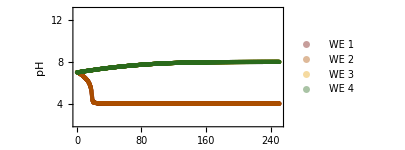

```mathematica
p1=ListPlot[Table[MapThread[{#1,#2}&,{timeList,Flatten[(out1[[3]]⟦All,WE⟦#,1⟧,WE⟦#,2⟧⟧&/@Range[Length[WE]])⟦i⟧,1]⟦All,1⟧}],{i,1,Length@WE}],AspectRatio->0.5,Frame-> True,FrameLabel-> {"Time(s)","pH"},PlotRange-> {All,{2,13}},
LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotStyle->plotStyle,PlotLegends-> Placed[LineLegend[{"WE 1", "WE 2","WE 3", "WE 4"},LegendLayout->"Row",Spacings-> {0.1,0.1}],{0.5,0.1}],ImageSize->300]
```

```mathematica
Vapp=out1[[1]];plotVoltage[nEl_,tC_]:=Block[{plotV,cnT,time},
cnT=Quotient[tC,tS]+1;
time=Mod[tC,tS];
plotV=Partition[Table[fVShift[{Vapp⟦cnT,1,i⟧,Vapp⟦cnT,2,i⟧},{λ,offSet},time],{i,nEl^2}],nEl]];
dataVoltage[nEl_,tC_]:=Block[{plotV,cnT,time},
cnT=Quotient[tC,tS]+1;
time=Mod[tC,tS];
plotV=Partition[Table[fVShift[{Vapp⟦cnT,1,i⟧,Vapp⟦cnT,2,i⟧},{λ,offSet},time],{i,nEl^2}],nEl]];
voltageData=Table[plotVoltage[nEl,t],{t,0,nSteps tS,0.1}];
```

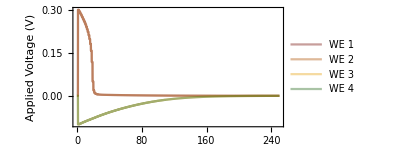

```mathematica
p2=ListPlot[Table[MapThread[{#1,#2}&,{Table[t,{t,0,nSteps tS,0.1}],voltageData[[All,WE[[i]][[1]],WE[[i]][[2]]]]}],{i,Length@WE}],PlotStyle->plotStyle,Frame-> True,Axes-> None,Joined->True,FrameLabel-> {"Time(s)","Applied Voltage (V)"},PlotRange->Full,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},AspectRatio->0.5,PlotLegends-> Placed[LineLegend[{"WE 1", "WE 2","WE 3", "WE 4"},LegendLayout->"Row",Spacings-> {0.1,0.1}],{0.5,0.9}],ImageSize->300]
```

```mathematica
solnS=out1[[2]];
```

```mathematica
timeList=Range[0.1,nSteps tS ,timeStep];
```

```mathematica
plotCurrent[nEl_,tC_]:=Block[{currentEL,cnT,time},
cnT=Quotient[tC,tS]+1;
time=Mod[tC,tS];
currentEL=(Evaluate[Table[(Symbol["iEL"<>ToString[i]<>"s"<>ToString[j]][t]),{i,nEl},{j,nEl}]/.solnS⟦cnT⟧])/.t->tC];
```

```mathematica
currentData=Table[plotCurrent[nEl,time],{time,0.1,nSteps tS,0.1}];
dataX=Table[currentData[[All,WE[[i,1]],WE[[i,2]]]],{i,Length@WE}];
```

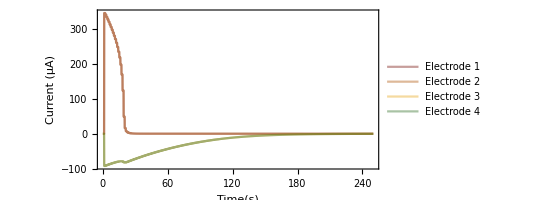

```mathematica
ListPlot[Table[MapThread[{#1,10^6#2}&,{timeList,dataX[[i]]}],{i,Length@WE}],PlotStyle->plotStyle,Frame-> True,Axes-> None,Joined->True,FrameLabel-> {"Time(s)","Current (μA)"},PlotRange->Full,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},AspectRatio->0.5,PlotLegends-> Placed[LineLegend[{"Electrode 1", "Electrode 2","Electrode 3", "Electrode 4"},Spacings-> {0.1,0.1}],{0.75,0.25}],ImageSize->400]
```

```mathematica
dataX=Table[currentData[[All,CE[[i,1]],CE[[i,2]]]],{i,Length@CE}];
```

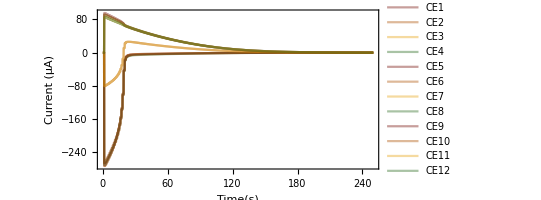

```mathematica
ListPlot[Table[MapThread[{#1,10^6#2}&,{timeList,dataX[[i]]}],{i,Length@CE}],PlotStyle->plotStyle,Frame-> True,Axes-> None,Joined->True,FrameLabel-> {"Time(s)","Current (μA)"},PlotRange->Full,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},AspectRatio->0.5,PlotLegends-> Placed[LineLegend[Table["CE"<>ToString[el],{el,Length@CE}],LabelStyle->12,LegendLayout->"Row",Spacings-> {0.15,0.15}],{0.5,0.15}],ImageSize->400]
```

```mathematica
cnTs=0;nSteps=50;
out2=electroChemAutomata[nEl,nSteps,{4,6,9,11},0.25,3.0];
```

```mathematica
tS=3.0;
```

```mathematica
timeList=Flatten@Table[Table[tC,{tC,tS cnTs, tS (cnTs+1),timeStep}],{cnTs,0,nSteps}];
```

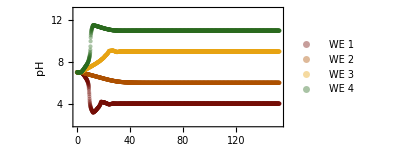

```mathematica
p3=ListPlot[Table[MapThread[{#1,#2}&,{timeList,Flatten[(out2[[3]]⟦All,WE⟦#,1⟧,WE⟦#,2⟧⟧&/@Range[Length[WE]])⟦i⟧,1]⟦All,1⟧}],{i,1,Length@WE}],AspectRatio->0.5,Frame-> True,FrameLabel-> {"Time(s)","pH"},PlotRange-> {All,{2,13}},
LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},PlotStyle->plotStyle,PlotLegends-> Placed[LineLegend[{"WE 1", "WE 2","WE 3", "WE 4"},LegendLayout->"Row",Spacings-> {0.1,0.1}],{0.5,0.1}],ImageSize->300]
```

```mathematica
Vapp=out2[[1]];plotVoltage[nEl_,tC_]:=Block[{plotV,cnT,time},
cnT=Quotient[tC,tS]+1;
time=Mod[tC,tS];
plotV=Partition[Table[fVShift[{Vapp⟦cnT,1,i⟧,Vapp⟦cnT,2,i⟧},{λ,offSet},time],{i,nEl^2}],nEl]];
dataVoltage[nEl_,tC_]:=Block[{plotV,cnT,time},
cnT=Quotient[tC,tS]+1;
time=Mod[tC,tS];
plotV=Partition[Table[fVShift[{Vapp⟦cnT,1,i⟧,Vapp⟦cnT,2,i⟧},{λ,offSet},time],{i,nEl^2}],nEl]];
voltageData=Table[plotVoltage[nEl,t],{t,0,nSteps tS,0.1}];
```

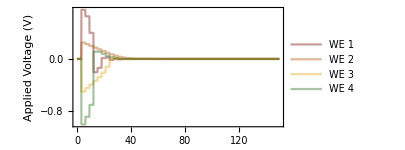

```mathematica
p4=ListPlot[Table[MapThread[{#1,#2}&,{Table[t,{t,0,nSteps tS,0.1}],voltageData[[All,WE[[i]][[1]],WE[[i]][[2]]]]}],{i,Length@WE}],PlotStyle->plotStyle,Frame-> True,Axes-> None,Joined->True,FrameLabel-> {"Time(s)","Applied Voltage (V)"},PlotRange->Full,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},AspectRatio->0.5,PlotLegends-> Placed[LineLegend[{"WE 1", "WE 2","WE 3", "WE 4"},LegendLayout->"Row",Spacings-> {0.1,0.1}],{0.5,0.9}],ImageSize->300]
```

```mathematica
solnS=out2[[2]];
```

```mathematica
timeList=Range[0.1,(nSteps )tS ,timeStep];
```

```mathematica
plotCurrent[nEl_,tC_]:=Block[{currentEL,cnT,time},
cnT=Quotient[tC,tS]+1;
time=Mod[tC,tS];
currentEL=(Evaluate[Table[(Symbol["iEL"<>ToString[i]<>"s"<>ToString[j]][t]),{i,nEl},{j,nEl}]/.solnS⟦cnT⟧])/.t->tC];
```

```mathematica
currentData=Table[plotCurrent[nEl,time],{time,0.1,nSteps tS,0.1}];
dataX=Table[currentData[[All,WE[[i,1]],WE[[i,2]]]],{i,Length@WE}];
```

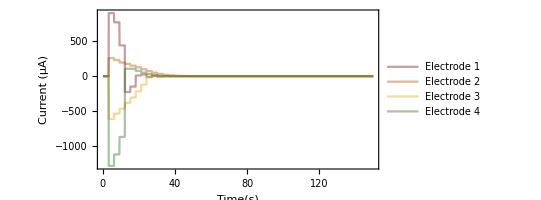

```mathematica
ListPlot[Table[MapThread[{#1,10^6#2}&,{timeList,dataX[[i]]}],{i,Length@WE}],PlotStyle->plotStyle,Frame-> True,Axes-> None,Joined->True,FrameLabel-> {"Time(s)","Current (μA)"},PlotRange->Full,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},AspectRatio->0.5,PlotLegends-> Placed[LineLegend[{"Electrode 1", "Electrode 2","Electrode 3", "Electrode 4"},Spacings-> {0.1,0.1}],{0.75,0.25}],ImageSize->400]
```

```mathematica
dataX=Table[currentData[[All,CE[[i,1]],CE[[i,2]]]],{i,Length@CE}];
```

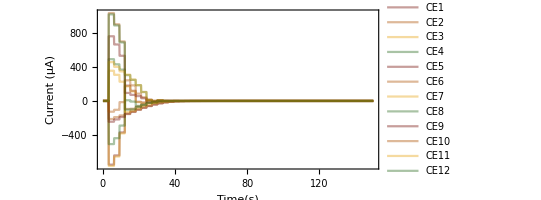

```mathematica
ListPlot[Table[MapThread[{#1,10^6#2}&,{timeList,dataX[[i]]}],{i,Length@CE}],PlotStyle->plotStyle,Frame-> True,Axes-> None,Joined->True,FrameLabel-> {"Time(s)","Current (μA)"},PlotRange->Full,LabelStyle->{Black,Directive[Black,FontColor->Black,FontSize->14]},AspectRatio->0.5,PlotLegends-> Placed[LineLegend[Table["CE"<>ToString[el],{el,Length@CE}],LabelStyle->12,LegendLayout->"Row",Spacings-> {0.15,0.15}],{0.5,0.85}],ImageSize->400]
```

```mathematica
Export[baseDirectory<>"pHControl4Elec_1.png",p1,ImageResolution->300]
```

/Users/abhisheksharma/Desktop/Hybrid_Computation_Final/pHControl4Elec_1.png

```mathematica
Export[baseDirectory<>"pHControl4Elec_2.png",p2,ImageResolution->300]
```

/Users/abhisheksharma/Desktop/Hybrid_Computation_Final/pHControl4Elec_2.png

```mathematica
Export[baseDirectory<>"pHControl4Elec_3.png",p3,ImageResolution->300]
```

/Users/abhisheksharma/Desktop/Hybrid_Computation_Final/pHControl4Elec_3.png

```mathematica
Export[baseDirectory<>"pHControl4Elec_4.png",p4,ImageResolution->300]
```

/Users/abhisheksharma/Desktop/Hybrid_Computation_Final/pHControl4Elec_4.png